Verification of the BAE off formulae for nondegenerate internal squeezing
And 4x4 combined readout

Verification of the BAE off formulae for nondegenerate internal squeezing

```mathematica
(*BAE adds in complications that are too much for this project, let's drop it
--> sanity check denominator which appears to requires ρBAE unlike dIS, re-do derivation with no BAE to make sure*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id; (*manually removed BAE: -(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}})*)
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 invMa-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];

Block[{noiseΔSx=Together[Sx[[2,2]]-1]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];]
Print["Sx = 1 + ",numerΔSx,"\n/\n",denomΔSx//Expand//FullSimplify,"\n"]

Block[{sigTsqr=Together[sigTransferAbs^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqr=Collect[Numerator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];
denomTsqr=Collect[Denominator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];]
Print["|T|^2 = ",numerTsqr,"\n/\n",denomTsqr]

Block[{ρRP=0},
Print[1+numerΔSx/denomΔSx//FullSimplify];
Print[numerTsqr/denomTsqr];
Print[Sh//FullSimplify];]

Sx/.{ωs->0,χ->γbtot x}//FullSimplify//MatrixForm
(*cf. nOPO:
({{1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4), 0}, {0, 1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4)}})*)
```

Xiang Li et al, 2020 code.

```mathematica
(*the code in this cell is from Xiang Li by personal correspondence, it is NOT my original work and my GitHub licence does not apply to it! -- James Gardner*)
solnsc=Solve[{
-I Ω A1==-γ A1 +Sqrt[2 γ]u1,
-I Ω A2 == -α/ℏ (X- L h)-γ A2 +Sqrt[2 γ]u2,
-I Ω X ==P/(M/4),
-I Ω P ==α A1},{A1,A2,X,P}];
v2outsc=u2-Sqrt[2γ]A2/.solnsc[[1]]//Simplify;
noise21sc=Coefficient[v2outsc,u1]//Simplify;
noise22sc=Coefficient[v2outsc,u2]//Simplify;
sigsc=Coefficient[v2outsc,h]//Simplify;
screp={γ->2 Pi 500.,ω0->2 Pi 3 10^8/(2 10^-6),ℏ->10^-34,Ω->2 Pi f,Pc->3 10^6,L->4000,c ->3 10^8,M->200};
qnoisesc=Sqrt[Abs[noise21sc]^2+Abs[noise22sc]^2]/Abs[sigsc]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.screp;
hsql=Sqrt[8ℏ/(M Ω^2 L^2)]/.screp;

soln=Solve[{
-I Ω B1== G C1 +Sqrt[2 γ] u1+ g A1 -(γ) B1,
-I Ω B2== - G C2  +Sqrt[2 γ] u2+g A2 -(γ) B2,
-I Ω C1 ==-γm C1+ G B1+Sqrt[2 γm] fc1,
-I Ω C2 ==-γm C2-G B2+Sqrt[2 γm] fc2,
-I Ω A1==- g B1,
-I Ω A2 == -g B2-α/ℏ (X- L h),
-I Ω X ==P/(M/4),
-I Ω P ==α A1},{A1,A2,B1,B2,C1,C2,X,P}];
v2out=u2-Sqrt[2γ]B2/.soln[[1]];
(*The WLC parts include:quantum noise only,thermal noise,and combined.*)
noise21=Coefficient[v2out,u1]//Simplify;
noise22=Coefficient[v2out,u2]//Simplify;
noise2t1=Coefficient[v2out,fc1]Sqrt[2kB Tenv/(ℏ ωm)]//Simplify;
noise2t2=Coefficient[v2out,fc2]Sqrt[2kB Tenv/(ℏ ωm)]//Simplify;
sig=Coefficient[v2out,h]//Simplify;
wlcrep={g->2 Pi 5000(*6000*),G->2 Pi 4930(*5950*),γ->2 Pi 500.,γm->2 Pi 10^8/( 2 8 10^9),ωm->2 Pi  10^8,ω0->2 Pi 3 10^8/(2 10^-6),ℏ->10^-34,Tenv->4,kB->1.38 10^-23,Ω->2 Pi f,Pc->3 10^6,L->4000,c ->3 10^8,M->200};
(*qnoisebase=Sqrt[Abs[noise21]^2+Abs[noise22]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.baserep;*)
qnoisewlc=Sqrt[Abs[noise21]^2+Abs[noise22]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
thnoisewlc=Sqrt[Abs[noise2t1]^2+Abs[noise2t2]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
totalnoisewlc=Sqrt[Abs[noise21]^2+Abs[noise22]^2+Abs[noise2t1]^2+Abs[noise2t2]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
hsql=Sqrt[8ℏ/(M Ω^2 L^2)]/.wlcrep;

(*noise and signal responses to use separately*)
liWLCQNResponse=Sqrt[Abs[noise21]^2+Abs[noise22]^2]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
liWLCSigResponse=Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;

(*clear all variables except for Li's functions*)
Clear@@DeleteCases[Names@"`*","hsql"|"qnoisesc"|"qnoisewlc"|"totalnoisewlc"|"liWLCQNResponse"|"liWLCSigResponse"];
```

4x4 combined readout

```mathematica
SetDirectory[NotebookDirectory[]];
(*4x4 solution
--> verifying RP and pump phase dependence (or lack thereof) of transfer functions
--> allows for combined signal-idler readout*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γbR>0,γctot≥γcR≥0,1>Rpd≥0,χ≥0,ωs≥0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals,ψ0∈Reals,ψ1∈Reals,ψ2∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id4=IdentityMatrix[4];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id4+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1, 0, 0}, {-1, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
invMa=Inverse[Ma]//Simplify;
(*diagonal matrices are not in the centre of the matrix algebra, only multiples of the identity are --> silly mistake!*)
Mb=({{γbtot, 0, 0, 0}, {0, γbtot, 0, 0}, {0, 0, γctot, 0}, {0, 0, 0, γctot}})-ⅈ Ω Id4+χ({{0, 0, 0, ⅈ Exp[ⅈ ϕ]}, {0, 0, -ⅈ Exp[-ⅈ ϕ], 0}, {0, ⅈ Exp[ⅈ ϕ], 0, 0}, {-ⅈ Exp[-ⅈ ϕ], 0, 0, 0}})+ωs^2({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ4=1/2^(1/2)({{1, 1, 0, 0}, {-ⅈ, ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, -ⅈ, ⅈ}});
Rin=Simplify[(1-Rpd)^(1/2)Γ4.(Id4-2 ({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}})).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Ra=Simplify[-(1-Rpd)^(1/2) 2ωs γa^(1/2) Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Rb=Simplify[-(1-Rpd)^(1/2)2Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{(γbtot-γbR)^(1/2), 0, 0, 0}, {0, (γbtot-γbR)^(1/2), 0, 0}, {0, 0, (γctot-γcR)^(1/2), 0}, {0, 0, 0, (γctot-γcR)^(1/2)}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[-(1-Rpd)^(1/2)2^(1/2)ωs (-ⅈ β)Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),TimeConstraint->TimeConstraint0]; (*last matrix is more like ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})*)
(*mixed readout, linear combination of all Xpd quadratures is possible,
Xcom = C24.Xpd, Xcom=({{Xcom1}, {Xcom2}}) is 2x1, Xpd=({{Xb1}, {Xb2}, {Xc1}, {Xc2}}) is 4x1, therefore C24 is 2x4,
ψ0=π/2 makes signal just Xb2 since Xb1 doesn't have GW signal (still might not be optimal) ψ1=ϕ maximises GW signal in idler but might not be overall optimal, ψ2=0 is signal readout, ψ2=π/2 is idler readout, anything in-between will have the transfer functions pick up on covariances introduced*)
C24=({{Cos[ψ2] Cos[ψ0], Cos[ψ2]Sin[ψ0], Sin[ψ2] Cos[ψ1], Sin[ψ2]Sin[ψ1]}, {-Sin[ψ2]Cos[ψ0], -Sin[ψ2]Sin[ψ0], Cos[ψ2] Cos[ψ1], Cos[ψ2] Sin[ψ1]}});

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.
FlipI);

(* signal readout is just SxCom with ψ0=π/2, ψ2=0;
Sx=Simplify[(
Rpd Id4
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb])/.ConjugateFlipI,TimeConstraint->{1,5}];
sigTransferAbs= Simplify[ComplexExpand[Abs[ Simplify[(T.({{1}, {1}, {0}, {0}}))[[2]][[1]],TimeConstraint->{1,5}]]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];*)

(*4x4 reduced down to 2x2 by combining readout quadratures, check this, is it clear that the uncorrelated vacuum assumption applies through the C24 matrices?*)
SxCom=Simplify[(
Rpd C24.ConjugateTranspose[C24]
+C24.Rin.ConjugateTranspose[Rin].ConjugateTranspose[C24]
+C24.Ra.ConjugateTranspose[Ra].ConjugateTranspose[C24]
+C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransferCom = Simplify[(C24.T.({{1}, {1}, {0}, {0}}))[[1]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbsCom= Simplify[ComplexExpand[Abs[sigTransferCom]],TimeConstraint->{1,5}];
ShCom=Simplify[SxCom[[1,1]]/sigTransferAbsCom^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
Sx44=Simplify[(
Rpd Id4
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb])/.ConjugateFlipI,TimeConstraint->{1,5}];
Simplify[Sx44[[1;;2,1;;2]]/.{ρRP->0},TimeConstraint->{0.1,1}]//MatrixForm
Simplify[Sx44[[3;;4,3;;4]]/.{ρRP->0},TimeConstraint->{0.1,1}]//MatrixForm
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

((8 γbR γctot χ^2 Ω^2-8 Rpd γbR γctot χ^2 Ω^2-2 γbtot γctot χ^2 Ω^2+χ^4 Ω^2+γctot^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γctot^2+Ω^2)+γa^2 (-8 (-1+Rpd) γbR γctot χ^2-2 γbtot γctot χ^2+χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γctot^2+Ω^2))-2 γctot^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2+γctot^2 ωs^4+Ω^2 ωs^4)/((ⅈ χ^2 Ω+γbtot (-ⅈ γctot-Ω) Ω-γctot Ω^2+ⅈ Ω^3-γa (-γbtot γctot+χ^2+ⅈ γbtot Ω+ⅈ γctot Ω+Ω^2)+γctot ωs^2-ⅈ Ω ωs^2) (-ⅈ χ^2 Ω+ⅈ γbtot (γctot+ⅈ Ω) Ω-γctot Ω^2-ⅈ Ω^3-γa (χ^2-γbtot (γctot+ⅈ Ω)-ⅈ γctot Ω+Ω^2)+γctot ωs^2+ⅈ Ω ωs^2)) | 0
0 | (8 γbR γctot χ^2 Ω^2-8 Rpd γbR γctot χ^2 Ω^2-2 γbtot γctot χ^2 Ω^2+χ^4 Ω^2+γctot^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γctot^2+Ω^2)+γa^2 (-8 (-1+Rpd) γbR γctot χ^2-2 γbtot γctot χ^2+χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γctot^2+Ω^2))-2 γctot^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2+γctot^2 ωs^4+Ω^2 ωs^4)/((ⅈ χ^2 Ω+γbtot (-ⅈ γctot-Ω) Ω-γctot Ω^2+ⅈ Ω^3-γa (-γbtot γctot+χ^2+ⅈ γbtot Ω+ⅈ γctot Ω+Ω^2)+γctot ωs^2-ⅈ Ω ωs^2) (-ⅈ χ^2 Ω+ⅈ γbtot (γctot+ⅈ Ω) Ω-γctot Ω^2-ⅈ Ω^3-γa (χ^2-γbtot (γctot+ⅈ Ω)-ⅈ γctot Ω+Ω^2)+γctot ωs^2+ⅈ Ω ωs^2)))

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

((-2 γbtot (4 (-1+Rpd) γcR+γctot) χ^2 Ω^2+χ^4 Ω^2+γctot^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γctot^2+Ω^2)+γa^2 (-2 γbtot (4 (-1+Rpd) γcR+γctot) χ^2+χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γctot^2+Ω^2))-2 γctot^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-(4 (-1+Rpd) γcR+γctot) χ^2+γbtot (γctot^2+Ω^2)) ωs^2+γctot^2 ωs^4+Ω^2 ωs^4)/((ⅈ χ^2 Ω+γbtot (-ⅈ γctot-Ω) Ω-γctot Ω^2+ⅈ Ω^3-γa (-γbtot γctot+χ^2+ⅈ γbtot Ω+ⅈ γctot Ω+Ω^2)+γctot ωs^2-ⅈ Ω ωs^2) (-ⅈ χ^2 Ω+ⅈ γbtot (γctot+ⅈ Ω) Ω-γctot Ω^2-ⅈ Ω^3-γa (χ^2-γbtot (γctot+ⅈ Ω)-ⅈ γctot Ω+Ω^2)+γctot ωs^2+ⅈ Ω ωs^2)) | 0
0 | (-2 γbtot (4 (-1+Rpd) γcR+γctot) χ^2 Ω^2+χ^4 Ω^2+γctot^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γctot^2+Ω^2)+γa^2 (-2 γbtot (4 (-1+Rpd) γcR+γctot) χ^2+χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γctot^2+Ω^2))-2 γctot^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-(4 (-1+Rpd) γcR+γctot) χ^2+γbtot (γctot^2+Ω^2)) ωs^2+γctot^2 ωs^4+Ω^2 ωs^4)/((ⅈ χ^2 Ω+γbtot (-ⅈ γctot-Ω) Ω-γctot Ω^2+ⅈ Ω^3-γa (-γbtot γctot+χ^2+ⅈ γbtot Ω+ⅈ γctot Ω+Ω^2)+γctot ωs^2-ⅈ Ω ωs^2) (-ⅈ χ^2 Ω+ⅈ γbtot (γctot+ⅈ Ω) Ω-γctot Ω^2-ⅈ Ω^3-γa (χ^2-γbtot (γctot+ⅈ Ω)-ⅈ γctot Ω+Ω^2)+γctot ωs^2+ⅈ Ω ωs^2)))

```mathematica
(*idler-idler covariance*)
Collect[Numerator[Together[Sx44[[3,4]]]],ρRP,Simplify]
Denominator[Together[Sx44[[3,4]]]]
(*signal-signal covariance*)
Sx44[[1,2]]
(*signal mixed readout*)
SxSigEqual=Together[1/2(Sx44[[1,1]]+Sx44[[2,2]]+Sx44[[1,2]]+Sx44[[2,1]])];
Collect[Numerator[SxSigEqual],{ρRP},FullSimplify]
```

2 ⅈ (-1+ⅇ^(4 ⅈ ϕ)) (-1+Rpd) γcR ρRP^2 χ^2 ωs^2 (γa (-2 γbtot γctot χ^2+χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γctot^2+Ω^2))+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-√2 (-1+Rpd) γcR ρRP χ^2 Ω^2 ωs^2 (-3 (1+ⅇ^(4 ⅈ ϕ)) γbtot^2 Ω^2 (γctot^2+Ω^2)+γa^2 ((1+ⅇ^(4 ⅈ ϕ)) γbtot^2 (γctot^2+Ω^2)-3 (1+ⅇ^(4 ⅈ ϕ)) (χ^4+γctot^2 Ω^2+2 χ^2 Ω^2+Ω^4)+2 γbtot ((1+ⅇ^(4 ⅈ ϕ)) γctot χ^2+4 ⅈ ⅇ^(2 ⅈ ϕ) γctot^2 Ω+4 ⅈ ⅇ^(2 ⅈ ϕ) Ω (χ^2+Ω^2)))+2 γbtot Ω ((1+ⅇ^(4 ⅈ ϕ)) γctot χ^2 Ω-4 ⅈ ⅇ^(2 ⅈ ϕ) γctot^2 (Ω^2-ωs^2)-4 ⅈ ⅇ^(2 ⅈ ϕ) Ω^2 (χ^2+Ω^2-ωs^2))+(1+ⅇ^(4 ⅈ ϕ)) (χ^4 Ω^2+(γctot^2+Ω^2) (Ω^2-ωs^2)^2+2 χ^2 (Ω^4-Ω^2 ωs^2))+2 γa (-4 γbtot γctot^2 Ω^2-4 γbtot χ^2 Ω^2-4 γbtot Ω^4+γbtot γctot^2 ωs^2+γctot χ^2 ωs^2+γbtot Ω^2 ωs^2+ⅇ^(4 ⅈ ϕ) (γctot χ^2 ωs^2+γbtot γctot^2 (-4 Ω^2+ωs^2)+γbtot Ω^2 (-4 χ^2-4 Ω^2+ωs^2))+4 ⅈ ⅇ^(2 ⅈ ϕ) Ω (-χ^4+γbtot^2 (γctot^2+Ω^2)-(γctot^2+Ω^2) (Ω^2-ωs^2)+χ^2 (-2 Ω^2+ωs^2))))

ⅇ^(2 ⅈ ϕ) Ω^4 (-ⅈ γa γbtot γctot+ⅈ γa χ^2-γa γbtot Ω-γa γctot Ω-γbtot γctot Ω+χ^2 Ω+ⅈ γa Ω^2+ⅈ γbtot Ω^2+ⅈ γctot Ω^2+Ω^3-ⅈ γctot ωs^2-Ω ωs^2)^2 (ⅈ γa γbtot γctot-ⅈ γa χ^2-γa γbtot Ω-γa γctot Ω-γbtot γctot Ω+χ^2 Ω-ⅈ γa Ω^2-ⅈ γbtot Ω^2-ⅈ γctot Ω^2+Ω^3+ⅈ γctot ωs^2-Ω ωs^2)^2

(2 ⅈ √2 (-1+Rpd) γbR ρRP (γctot+ⅈ Ω) ωs^2 (3 ⅈ γctot χ^2 Ω-γctot^2 Ω^2-χ^2 Ω^2-Ω^4+γa γbtot (γctot^2+Ω^2)+ⅈ γbtot Ω (γctot^2+Ω^2)+ⅈ γa (5 ⅈ γctot χ^2+γctot^2 Ω+χ^2 Ω+Ω^3)+γctot^2 ωs^2+Ω^2 ωs^2))/(Ω^2 (γa γbtot (-ⅈ γctot-Ω)+χ^2 Ω-γbtot (γctot-ⅈ Ω) Ω+ⅈ γctot Ω^2+Ω^3+ⅈ γa (χ^2+Ω (ⅈ γctot+Ω))-ⅈ γctot ωs^2-Ω ωs^2) (χ^2 Ω-γbtot (γctot+ⅈ Ω) Ω-ⅈ γctot Ω^2+Ω^3-ⅈ γa (χ^2-γbtot (γctot+ⅈ Ω)-ⅈ γctot Ω+Ω^2)+ⅈ γctot ωs^2-Ω ωs^2)^2)

-4 (-1+Rpd) γbR ρRP^2 (γctot^2+Ω^2) ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)+Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4) ((γa^2+Ω^2) (-8 (-1+Rpd) γbR γctot χ^2-2 γbtot γctot χ^2+γctot^2 Ω^2+γbtot^2 (γctot^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)+2 √2 (-1+Rpd) γbR ρRP Ω^2 ωs^2 (8 γa γctot χ^2 Ω^2 (γctot^2+χ^2+Ω^2)+γa^2 (5 γctot^2 χ^4+(γctot^2+χ^2)^2 Ω^2+2 (γctot^2+χ^2) Ω^4+Ω^6-6 γbtot γctot χ^2 (γctot^2+Ω^2)+γbtot^2 (γctot^2+Ω^2)^2)+Ω^2 (-3 γctot^2 χ^4+(γctot^2+χ^2)^2 Ω^2+2 (γctot^2+χ^2) Ω^4+Ω^6+2 γbtot γctot χ^2 (γctot^2+Ω^2)+γbtot^2 (γctot^2+Ω^2)^2)-2 Ω^2 (γctot^2+Ω^2) (γctot^2+χ^2+Ω^2) ωs^2+2 γa (γctot^2+Ω^2) (-3 γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2+(γctot^2+Ω^2)^2 ωs^4)

```mathematica
(*fix angles*)
signalReadout={ψ0->π/2,ψ2->0};
idlerReadout={ϕ->π/2,ψ1->(*=ϕ=*)π/2,ψ2->π/2};

(*signal function retains total freedom in four angles: ϕ,ψ0,ψ1,ψ2*)
Block[{sigTsqrCom=Together[sigTransferAbsCom^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqrCom=Collect[Numerator[sigTsqrCom],{ϕ,ρRP},SimplifyConstrained];
denomTsqrcom=Collect[Denominator[sigTsqrCom],{ϕ,ρRP},SimplifyConstrained];]
sigTsqrComSimpl=numerTsqrCom/denomTsqrcom;
Clear[numerTsqrCom,denomTsqrcom]

(*simplifying idler and signal readout noise functions separately, too complex otherwise*)
Block[{noiseΔSx=Together[-1+SxCom[[1,1]]/.signalReadout]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx4x4=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx4x4=Collect[Denominator[noiseΔSx]//Expand//Simplify,{ϕ,ρRP},SimplifyConstrained];]
SxSignal=1+numerΔSx4x4/denomΔSx4x4;
Clear[numerΔSx4x4,denomΔSx4x4]
(*I verified that ρRP does not appear in the denominator for nIS*)

(*fast plotter assumes /.{ψ0->π/2(*only Xb2*),ψ1->ϕ(*best idler for GW signal but not noise*),ψ2->π/2(*idler readout*)}/.ϕ->π/2*)
Block[{noiseΔSxComNoFree=Together[-1+SxCom[[1,1]]/.idlerReadout]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSxComNoFree=Collect[Numerator[noiseΔSxComNoFree],{ϕ,ρRP},SimplifyConstrained];
denomΔSxComNoFree=Collect[Denominator[noiseΔSxComNoFree]//Expand//Simplify,{ϕ,ρRP},SimplifyConstrained];]
SxIdler=1+numerΔSxComNoFree/denomΔSxComNoFree;
Clear[numerΔSxComNoFree,denomΔSxComNoFree]

(*compare signal and idler readouts*)
Print["combined readout, sig. transfer fn.: \n","|T|^2 = ",sigTsqrComSimpl]
Print["signal readout (for ψ0=π/2, ψ2=0): \n","Sx = ",SxSignal,"\n|T|^2 = ",sigTsqrComSimpl/.signalReadout]
Print["idler readout (for ψ1=ϕ=π/2, ψ2=π/2): \n","Sx = ",SxIdler,"\n|T|^2 = ",sigTsqrComSimpl/.idlerReadout]

ShSignal=SxSignal/(sigTsqrComSimpl/.signalReadout)//Simplify;(*=ShCom/.signalReadout, should check this?*)
ShIdler=SxIdler/(sigTsqrComSimpl/.idlerReadout)//Simplify; (*==ShCom/.idlerReadout*)

(*assume that perfect, frequency-dependant external squeezing is available such that the shot noise from the readout port in signal and idler is reduced by 10 dB
--> check that this assumption is valid*)
SxComExtSqz11SignalRO=Simplify[((
Rpd C24.ConjugateTranspose[C24]
+extSqzFactor C24.Rin.ConjugateTranspose[Rin].ConjugateTranspose[C24]
+C24.Ra.ConjugateTranspose[Ra].ConjugateTranspose[C24]
+C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])[[1,1]]/.ConjugateFlipI)/.signalReadout,TimeConstraint->{1,5}];
ShComExtSqzSignalRO=Simplify[SxComExtSqz11SignalRO/(sigTsqrComSimpl/.signalReadout),TimeConstraint->{1,5}];
SxComExtSqz11IdlerRO=Simplify[((
Rpd C24.ConjugateTranspose[C24]
+extSqzFactor C24.Rin.ConjugateTranspose[Rin].ConjugateTranspose[C24]
+C24.Ra.ConjugateTranspose[Ra].ConjugateTranspose[C24]
+C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])[[1,1]]/.ConjugateFlipI)/.idlerReadout,TimeConstraint->{1,5}];
ShComExtSqzIdlerRO=Simplify[SxComExtSqz11IdlerRO/(sigTsqrComSimpl/.idlerReadout),TimeConstraint->{1,5}];
```

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

combined readout, sig. transfer fn.: 
|T|^2 = -(4 (-1+Rpd) β^2 ωs^2 (γbR (γctot^2+Ω^2) Cos[ψ2]^2 Sin[ψ0]^2+χ Cos[ϕ-ψ1] (γcR χ Cos[ϕ-ψ1] Sin[ψ2]^2-√(γbR γcR) γctot Sin[ψ0] Sin[2 ψ2])))/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

signal readout (for ψ0=π/2, ψ2=0): 
Sx = 1+(-8 (-1+Rpd) γbR ρRP^2 (γctot^2+Ω^2) ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-8 (-1+Rpd) γbR γctot χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4))/(Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2)
|T|^2 = -(4 (-1+Rpd) β^2 γbR (γctot^2+Ω^2) ωs^2)/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

idler readout (for ψ1=ϕ=π/2, ψ2=π/2): 
Sx = 1+(-8 (-1+Rpd) γcR ρRP^2 χ^2 ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-8 (-1+Rpd) γcR χ^2 Ω^4 (γbtot (γa^2+Ω^2)+γa ωs^2) ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4))/(Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2)
|T|^2 = -(4 (-1+Rpd) β^2 γcR χ^2 ωs^2)/((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
ShSignal/.{ρRP->0}//FullSimplify
```

-1/(4 (-1+Rpd) β^2 γbR (γctot^2+Ω^2) ωs^2)((γa^2+Ω^2) (-8 (-1+Rpd) γbR γctot χ^2-2 γbtot γctot χ^2+γctot^2 Ω^2+γbtot^2 (γctot^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)

```mathematica
(ShSignal/.{ρRP->0}//FullSimplify)/.{Ω->√((-γa^2 (γbtot+γctot)-γa ωs^2+γctot ωs^2)/(γbtot+γctot)),χ->√((γa+γbtot) (γa+γctot+ωs^2/(γbtot+γctot)))}//Simplify
```

(2 (γa+γbtot) γctot)/(β^2 (γbtot+γctot))

```mathematica
equalReadout={ϕ->π/2,ψ0->π/2,ψ1->(*ϕ=*)π/2,ψ2->π/4};
ΔSxEqual=Together[-1+SxCom[[1,1]]/.equalReadout];
denomΔSxEqual=Denominator[ΔSxEqual]//Expand//FullSimplify
```

Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*copying plotting functions from nIS_RP.nb, modifying for new parameters*)
```

```mathematica
(*physical constants*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);

setDerivedParams1[]:=(
τRoundTripArm=(2 Larm)/c;
τRoundTripSRC=(2Lsrc)/c;
γbR=-1/(2 τRoundTripSRC)Log[1-Tsrm];
γcR=γbR;(*default to symSRM*)
(*an approximation when ωs<<ωFSR=1/τRoundTripArm*)
ωs=c(Titm/(4 Lsrc Larm))^(1/2);
(*using formula for G from Korobko*)(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match β=(αGW Larm)/(2^(1/2)ℏ), which is ((Pcirc Larm ω0)/(ℏ c))^(1/2) if αGW from Li is used --> factor of two missing? this is unresolved, but just use β=-G s.t. ahatdot=...+iGh or ...-iβh;
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm| --> β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);*)
(*!changing now to use Li formula for comparison to sWLC, why do these two disagree? I do not know.*)
β=((Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
(*(2^(1/2)ℏ β^2)/(Larm^2 μ)*)
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2;)

setConfigParamsCustom[λ00_,Larm0_,Lsrc0_,Pcirc0_,Titm0_,Tsrm0_,M0_,paramSetName0_:None,γcR0_:None,γbR0_:None,ωs0_:None]:=(
Clear[paramSetName,λ0,Larm,Lsrc,Pcirc,Titm,Tsrm,M,τRoundTripArm,τRoundTripSRC,γbR,γcR,ωs,β,μ,ρ];
(*manually set parameters, all in base SI units*)
paramSetName=If[paramSetName0===None,"Custom parameter set",paramSetName0];
λ0=λ00(*m*);ω0=2π c/λ0;
Larm=Larm0(*m*);
(*can be omitted if γbR and Tsrm are specified*)
Lsrc=If[Lsrc0===None,Lsrc ,Lsrc0(*m*)];
Pcirc=Pcirc0(*W*);
(*can be omitted if ωs is specified*)
Titm=If[Titm0===None,Titm,Titm0];
Tsrm=Tsrm0;
M=M0(*kg*);
setDerivedParams1[];
(*if specified, then override γbR and ωs*)
If[Not[γbR0===None],γbR=γbR0];
If[Not[γcR0===None],γcR=γcR0];
If[Not[ωs0===None],ωs=ωs0];
(*if unspecified, then use γbR or γcR (if γbR==0) and Tsrm to find τRoundTripSRC*)
If[Lsrc0===None,If[γbR==0,τRoundTripSRC=-1/(2 γcR)Log[1-Tsrm],τRoundTripSRC=-1/(2 γbR)Log[1-Tsrm]]
(*Print["inferred Lsrc (in m) = ",c τRoundTripSRC/2,"\n"];*);];
(*!changing now to use Li formula for comparison to sWLC, why do these two disagree? I do not know.*)
β=((Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2(*=(2^(1/2)ℏ β^2)/(Larm^2 μ)*);)

(*different interferometer parameter sets*)
(*λ00_,Larm0_,Lsrc0_,Pcirc0_,Titm0_,Tsrm0_,M0_,paramSetName0_:None,γcR0_:None,γbR0_:None,ωs0_:None*)
(*parameters of Advanced LIGO, from Adya et al, 2020 and https://dcc.ligo.org/public/0000/T0900043/011/LIGO-T0900043-11.pdf*)
setConfigParamsALIGO[]:=setConfigParamsCustom[1064. 10^-9(*m*),4. 10^3(*m*),56.(*m*),750. 10^3 (*W*),0.014,0.325,40.(*kg*),"Advanced LIGO",0(*=γcR*)]

(*parameters of LIGO Voyager, from Adhikari et al, 2020*)
setConfigParamsVoyager[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),56.(*m*)(*I assume that the upgrade is not changing Lsrc, which is not made obvious anywhere*),3. 10^6 (*W*),0.002,0.046,200.(*kg*),"LIGO Voyager",0(*=γcR*)]

(*parameters of NEMO, from Ackley et al, 2020*)
setConfigParamsNEMO[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),354.(*m*), 4.5 10^6(*W*),0.014,0.048,74.1(*kg*),"NEMO",0(*=γcR*)]

(*parameters from Korobko et al, 2019: "benchmark 3rd generation detector"*)
setConfigParamsKorobko2019[]:=setConfigParamsCustom[1550. 10^-9(*m*),20. 10^3(*m*),56.(*m*),4. 10^6(*W*),0.07,0.35,200.(*kg*),"Korobko et al, 2019",0(*=γcR*)]

(*parameters from Li et al, 2020 - NB:ωs and γR are not from LIGO Voyager!*)
setConfigParamsLi2020[γbR0_:None]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None,3. 10^6(*W*),None,0.046(*assuming LIGO Voyager's Subscript[T, SRM] was used for γR*),200.(*kg*),"Li et al, 2020",0(*=γcR*),If[γbR0===None,2π 500.(*Hz*),γbR0],2π 5000.(*Hz*)]

printParams[]:=Print[StringForm[
"configuration parameters:\nparamSetName=``, λ0=`` m, Larm=`` km, Lsrc=`` m, Pcirc=`` MW, Titm=``, Tsrm=``, M=`` kg\nderived parameters:\nωFSR/(2  π)=1/τRoundTripArm=`` kHz, 1/τRoundTripSRC=`` kHz, γbR/(2  π)=`` kHz, γcR/(2  π)=`` kHz, ωs/(2  π)=`` kHz; ωs/γbR=``",paramSetName,NumberForm[λ0],NumberForm[Larm 10^-3],NumberForm[Lsrc],NumberForm[Pcirc 10^-6],NumberForm[Titm],NumberForm[Tsrm],NumberForm[M],NumberForm[1/τRoundTripArm 10^-3,3],NumberForm[1/τRoundTripSRC 10^-3,3],NumberForm[γbR/(2π)10^-3,3],NumberForm[γcR/(2π)10^-3,3],NumberForm[ωs/(2π)10^-3,3],NumberForm[ωs/γbR]]]
χRatio0=0.95;
Tla0=100. 10^-6(*=100ppm, arm cavity loss port*);
Tlb0=1000. 10^-6(*=1000ppm, signal SRC loss port*);
Tlc0=1000. 10^-6(*=1000ppm, idler SRC loss port*); (*along with symSRM=True as the default from now on*)
Rpd0=0.1(*=10%*);
```

```mathematica
(*loss functions, symSRM removed -- freedom now captured in γcR*)
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γbR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γctotFn[Tlc_]:=γcR+-1/(2 τRoundTripSRC)Log[1-Tlc]

(*fast plotters, with formulae simplified by fixing angles (no ϕ,ψ freedom)*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
singleReadoutSub[quantity_,varsList_?(VectorQ[#,NumericQ]&)]:=quantity/.{Ω->varsList[[1]],χ->varsList[[2]],γa->γaFn[varsList[[3]]],γbtot->γbtotFn[varsList[[4]]],γctot->γctotFn[varsList[[5]]],Rpd->varsList[[6]],ρRP->If[varsList[[7]]==1,ρ,0]}
QNSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[SxSignal]],varsList]
sigSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[sigTsqrComSimpl/.signalReadout]],varsList]
ASDShSignalReadout[varsList_]:=singleReadoutSub[Re[Sqrt[ShSignal]],varsList]
QNIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[SxIdler]],varsList]
sigIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[sigTsqrComSimpl/.idlerReadout]],varsList]
ASDShIdlerReadout[varsList_]:=singleReadoutSub[Re[Sqrt[ShIdler]],varsList]

(*slow formulae, with angles unfixed*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
comReadoutSub[quantity_,varsList_?(VectorQ[#,NumericQ]&)]:=quantity/.{Ω->varsList[[1]],χ->varsList[[2]],γa->γaFn[varsList[[3]]],γbtot->γbtotFn[varsList[[4]]],γctot->γctotFn[varsList[[5]]],Rpd->varsList[[6]],ρRP->If[varsList[[7]]==1,ρ,0],ϕ->varsList[[8]],ψ0->varsList[[9]],ψ1->varsList[[10]],ψ2->varsList[[11]]}
QNComReadout[varsList_]:=comReadoutSub[Re[Sqrt[SxCom[[1,1]]]],varsList]
sigComReadout[varsList_]:=comReadoutSub[Re[Sqrt[sigTsqrComSimpl]],varsList]
ASDShComReadout[varsList_]:=comReadoutSub[Re[Sqrt[ShCom]],varsList]

(*use nIS singularity threshold since denominators are the same regardless of readout*)
singularityThr[Tla_,Tlb_,Tlc_]:=(
poleSol0={{Ω->0,χ->√(γctot (γbtot+ωs^2/γa))},
{Ω->√((-γa^2 (γbtot+γctot)-γa ωs^2+γctot ωs^2)/(γbtot+γctot)),χ->√((γa+γbtot) (γa+γctot+ωs^2/(γbtot+γctot)))}};

If[Tla≠0,Min[χ/.poleSol0/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γctot->γctotFn[Tlc]}],χ/.poleSol0[[2]]/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γctot->γctotFn[Tlc]}])
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
legendStylerSingleReadout[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm, T_(l, c)=``ppm, R_PD=``, ρ``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],If[vals0[[6]]==1,"≠0","=0"]],FontFamily->"Monospace"]
legendStylerSingleReadoutSplit[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm,\nT_(l, c)=``ppm, R_PD=``, ρ``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],If[vals0[[6]]==1,"≠0","=0"]],FontFamily->"Monospace"]
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
legendStylerComReadout[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm, T_(l, c)=``ppm, R_PD=``, ρ``, ϕ=``, ψ_0=``, ψ_1=``, ψ_2=``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],If[vals0[[6]]==1,"≠0","=0"],NumberForm[vals0[[7]]],NumberForm[vals0[[8]]],NumberForm[vals0[[9]]],NumberForm[vals0[[10]]]],FontFamily->"Monospace"]
legendStylerComReadoutSplit[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm,\nT_(l, c)=``ppm, R_PD=``, ρ``,\nϕ=``, ψ_0=``, ψ_1=``, ψ_2=``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[2]],vals0[[3]],vals0[[4]]],2]],4],NumberForm[N[vals0[[2]] 10^6]],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]]]],If[vals0[[6]]==1,"≠0","=0"],NumberForm[vals0[[7]]],NumberForm[vals0[[8]]],NumberForm[vals0[[9]]],NumberForm[vals0[[10]]]],FontFamily->"Monospace"]
```

```mathematica
plotwReadout[varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4}]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"nondegenerate internal squeezing\nparameters of "<>paramSetName<>"\nreadout: "<>readoutStr,plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotLegends->LineLegend[Join[Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[varsListList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])

plotγbcRGrid[configParams_(*γcR,γbR don't matter*),γRList_(*{{γcR1,γbR1},...}*),varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotStyle_:{},fRange_:{10,10^5}]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
{p1List,p2List,p3List}={{},{},{}};
Do[
setConfigParamsCustom@@ReplacePart[configParams,{-3->γRList[[j]][[1]],-2->γRList[[j]][[2]]}];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->250,
ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed",Epilog->Text[Style[StringForm["γcR/(2  π)=`` kHz\nγbR/(2  π)=`` kHz",NumberForm[(γRList[[j]][[1]])/(2π)10^-3],NumberForm[(γRList[[j]][[2]])/(2π)10^-3]],10,FontFamily->"Monospace"],Scaled[{0.75,0.65}],Background->Opacity[0.5,Lighter[LightGray]]]];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{All,1}},PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[varsListList]+1->Bottom},Frame->True,
PerformanceGoal->"Speed"];
AppendTo[p1List,p1];
AppendTo[p2List,p2];
AppendTo[p3List,p3];
,{j,1,Length[γRList]}];
Labeled[Grid[{p1List,p2List,p3List},Spacings->0],{"nondegenerate internal squeezing\nparameters of "<>paramSetName<>"\nreadout: "<>readoutStr,Grid[{{"", "signal", "quantum noise"}, {"sensitivity (NSR)", "transfer function", "transfer function"}, {"/ Hz^(-1/2) (log scale)", "/ [?] (log scale)", "/ dB (20 log_10)"}},Spacings->3],Grid[{{"frequency, f=Ω/(2  π) / Hz (log scale)"},{Framed[LineLegend[({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),Join[Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],FrameStyle->Thin]}}]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->Directive[12,FontFamily->"Calibri Light"]])

Clear[plotwReadoutPretty]
plotwReadoutPretty[varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:100,legendLabels_:None]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{leftPad,10},{1,All}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",14],},{,plotLabel}},
PerformanceGoal->performanceGoal,GridLines->{{},{0}}];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{1,1}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,20,25}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}}(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*),FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",14],},{,}},
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{All,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}}];
Labeled[Column[{p1,p2,p3},Spacings->0],
{LineLegend[plotStyle,
If[legendLabels===None,Table[If[readoutStr=="combined",legendStylerComReadoutSplit,legendStylerSingleReadoutSplit][varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels],LabelStyle->Directive[13],LegendMarkerSize->{{25,15}}]},{Right}])

plotSensPretty[varsListList_,readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:100,legendLabels_:None]:=(
{fmin,fmax}=fRange;
ShFn=
If[readoutStr=="signal",ASDShSignalReadout,
If[readoutStr=="idler",ASDShIdlerReadout,
If[readoutStr=="combined",ASDShComReadout,Throw["plotwReadout: readoutStr not recognised"]]]];
p3=LogLogPlot[Evaluate[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->450,ImagePadding->{{leftPad,10},{All,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}}];
Labeled[p3,
{LineLegend[plotStyle,
If[legendLabels===None,Table[If[readoutStr=="combined",legendStylerComReadoutSplit,legendStylerSingleReadoutSplit][varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels],LabelStyle->Directive[13],LegendMarkerSize->{{25,15}}]},{Right}])

plotγbcRSensRow[configParams_(*γcR,γbR don't matter*),γRList_(*{{γcR1,γbR1},...}*),varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotStyle_:{},fRange_:{2,9 10^4},SRange_:{3 10^-25,9 10^-21},sensTarget_:True,imageSize_:150,performanceGoal_:"Speed"]:=(
{fmin,fmax}=fRange;
ShFn=If[readoutStr=="signal",ASDShSignalReadout,If[readoutStr=="idler",ASDShIdlerReadout,If[readoutStr=="combined",ASDShComReadout,Throw["plotwReadout: readoutStr not recognised"]]]];
p3List={};
Do[
setConfigParamsCustom@@ReplacePart[configParams,{-3->γRList[[j]][[1]],-2->γRList[[j]][[2]]}];
p3=LogLogPlot[Evaluate[
If[sensTarget,
Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}],
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->{Automatic,imageSize},ImagePadding->If[j==1,{{45,7},{All,1}},{{1,7},{All,1}}],PlotStyle->If[sensTarget,({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Gray,DotDashed]}]),plotStyle],PlotRange->{fRange,SRange},Filling->If[sensTarget,{Length[varsListList]+1->Bottom},None],Frame->True,FrameTicksStyle->Directive[14],
PerformanceGoal->performanceGoal,Epilog->Text[Style[StringForm["(γ_(b, R))/(2  π)=``kHz\n(γ_(c, R))/(2  π)=``kHz",NumberForm[(γRList[[j]][[2]])/(2π)10^-3],NumberForm[(γRList[[j]][[1]])/(2π)10^-3]],14,FontFamily->"Monospace"],Scaled[{0.70,0.75}],Background->Opacity[0.5,Lighter[LightGray]]]];
AppendTo[p3List,p3];
,{j,1,Length[γRList]}];
Labeled[Grid[{p3List},Spacings->0],{"sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",Grid[{{"frequency, f=Ω/(2  π) / Hz (log scale)"},{Framed[LineLegend[If[sensTarget,({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[varsListList],Length[plotStyle]],{0,Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Gray,DotDashed]}]),plotStyle],
If[sensTarget,
Join[Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],Table[If[readoutStr=="combined",legendStylerComReadout,legendStylerSingleReadout][varsListList[[i]]],{i,1,Length[varsListList]}]],LabelStyle->Directive[14],LegendMarkerSize->{{25,15}}],FrameStyle->Thin]}}]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[14,FontFamily->"Calibri Light"]])

monoS[str_]:=Style[str,FontFamily->"Monospace"]

(*SetOptions[LogLinearPlot,BaseStyle->FontSize->16];*)
Clear[plotSensPretty]
plotSensPretty[varsListList_(*make sure that length matches the readout type*),readoutStr_,plotStyle_:{},fRange_:{2,9 10^4},plotRange_:{All,All},legendLabels_:None,legendTitle_:None,clipPlotStyleForLegend_:False,innerLegend_:False,innerLegendPos_:{0.5,0.7},performanceGoal_:"Quality",imageSize_:350]:=(
{fmin,fmax}=fRange;
ShFn=If[readoutStr=="signal",ASDShSignalReadout,If[readoutStr=="idler",ASDShIdlerReadout,If[readoutStr=="combined",ASDShComReadout,Throw["plotwReadout: readoutStr not recognised"]]]];
LogLogPlot[Evaluate[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->imageSize,PlotStyle->plotStyle,PlotRange->{{fmin,fmax},plotRange},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},PlotLegends->
If[innerLegend,Placed[LineLegend[If[clipPlotStyleForLegend,plotStyle[[2;;]],plotStyle],If[legendLabels===None,Table[(*combined readout legend not set up*)legendStylerSingleReadout[varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels]
,LabelStyle->Directive[14],LegendMarkerSize->{{25,15}},LegendLabel->legendTitle,Spacings->0.15],innerLegendPos],
LineLegend[If[clipPlotStyleForLegend,plotStyle[[2;;]],plotStyle],If[legendLabels===None,Table[legendStylerSingleReadout[varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels]
,LabelStyle->Directive[14],LegendMarkerSize->{{25,15}},LegendLabel->legendTitle]]])

Clear[plotwReadoutCompact]
plotwReadoutCompact[varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:100,legendLabels_:None,legendTitle_:None,legendPos_:{0.5,0.7}]:=(
{fmin,fmax}=fRange;
imageHeight=150;
bottomPad=55;
rightPad=11;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight},
ImagePadding->{{leftPad,rightPad},{1,1}},FrameTicksStyle->{{Directive[Black],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",16,Black],},{,}},
PerformanceGoal->performanceGoal,GridLines->{{},{0}}];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight+bottomPad},ImagePadding->{{leftPad,rightPad},{bottomPad,1}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,20,30}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}}(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*),FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",Black],},{Style["frequency / Hz",Black],}},
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->{Automatic,2imageHeight+bottomPad},AspectRatio->1/1.3,ImagePadding->{{leftPad+15,rightPad},{bottomPad,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",Black],},{Style["frequency / Hz",Black],}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},PlotLegends->Placed[LineLegend[plotStyle,
If[legendLabels===None,Table[If[readoutStr=="combined",legendStylerComReadoutSplit,legendStylerSingleReadoutSplit][varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels],LegendLabel->legendTitle,LabelStyle->Directive[18],LegendMarkerSize->{{25,15}},Spacings->0.15],legendPos]];
Grid[{{p1,Item[p3,Alignment->Center]},{p2,SpanFromAbove}},Spacings->0(*,Frame->All*)])
```

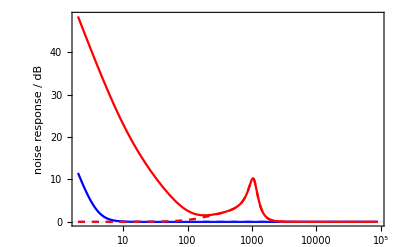
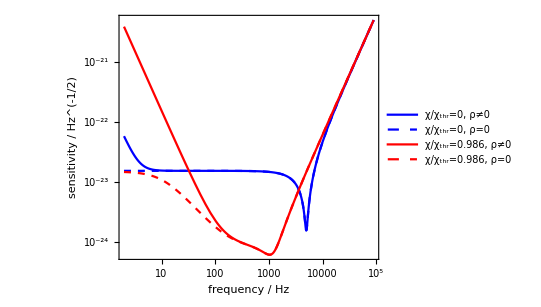
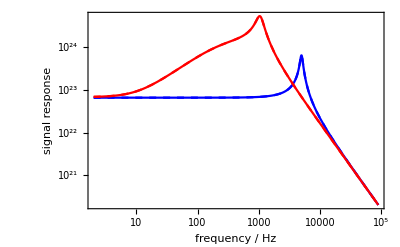
-Graphics- | -Graphics-
-Graphics- |

```mathematica
setConfigParamsLi2020[]
(*printParams[]
Print["inferred Lsrc (in m) = ",c τRoundTripSRC/2]
Print["T_ITM=",4 Lsrc Larm(ωs/c)^2/Lsrc c τRoundTripSRC/2]*)

(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
valsListList1={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{0,Tla0,Tlb0,Tlc0,Rpd0,0},
{4.93/5 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{4.93/5 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0}};

SetOptions[LogLinearPlot,BaseStyle->FontSize->18];
SetOptions[LogLogPlot,BaseStyle->FontSize->18];
grid=plotwReadoutCompact[valsListList1,"signal",None,{Blue,{Blue,Dashed},Red,{Red,Dashed}},{2,9 10^4},"Quality",{{All,49},{1.1 10^20,All},{All,All}},65,{Style["χ/χ_thr=0, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0, ρ=0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ=0",FontFamily->"Monospace"]}];
grid//Print
SetDirectory[NotebookDirectory[]];
(*Export is not working, use Print and save selection manually*)
(*Export["test.pdf",%];*)
(*Export["nIS_N_S_NSR.pdf",%%,"AllowRasterization"->False];*)
```

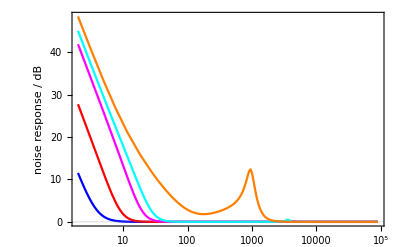
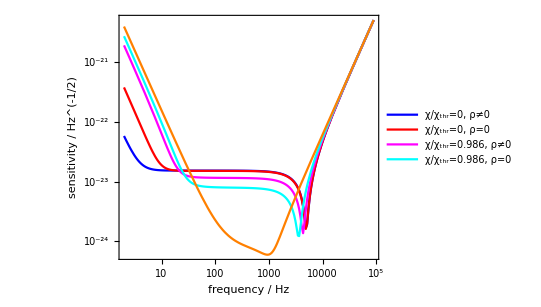
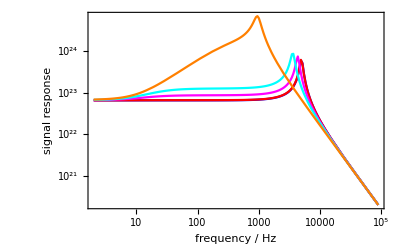
-Graphics- | -Graphics-
-Graphics- |

```mathematica
valsListList1={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{0.1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{0.5 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{0.7HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{0.99 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};

plotwReadoutCompact[valsListList1,"signal",None,{Blue,Red,Magenta,Cyan,Orange},{2,9 10^4},"Speed",{{All,49},{1.1 10^20,All},{All,All}},65,{Style["χ/χ_thr=0, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0, ρ=0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ=0",FontFamily->"Monospace"]}]
```

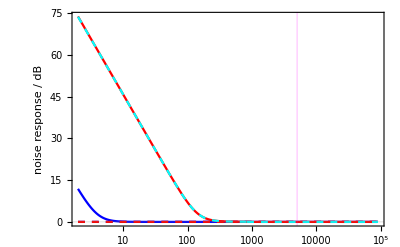
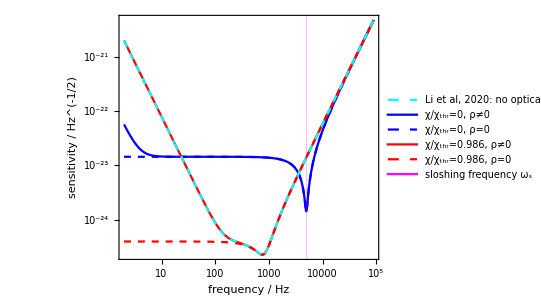
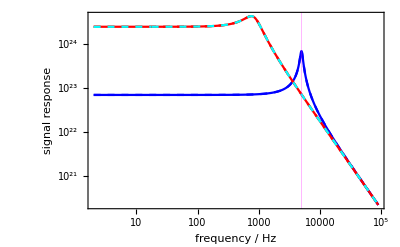
-Graphics- | -Graphics-
-Graphics- |

```mathematica
(*lossless*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020",0,2 π 500.,2 π 5000.]
Clear[plotwLosslessLimit]
plotwLosslessLimit[varsListList_(*make sure that length matches the readout type*),plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality"]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}={QNSignalReadout,sigSignalReadout,ASDShSignalReadout};
p1=LogLinearPlot[Evaluate[Join[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}],{20Log10[liWLCQNResponse]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{100,10},{1,All}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",14],},{,}},
PerformanceGoal->performanceGoal,GridLines->{{{ωs/(2π),Magenta}},{0}}];
p2=LogLogPlot[Evaluate[Join[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],{liWLCSigResponse}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{1,1}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},{1.1 10^20,All}},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",14],},{,}},
PerformanceGoal->performanceGoal,GridLines->{{{ωs/(2π),Magenta}},{}}];
p3=LogLogPlot[Evaluate[Join[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],{qnoisewlc}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},{All,9.9 10^-21}},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}},GridLines->{{{ωs/(2π),Magenta}},{}}];
Labeled[Column[{p1,p2,p3},Spacings->0],
{LineLegend[plotStyle,(*Join[Table[legendStylerSingleReadoutSplit[varsListList[[i]]],{i,1,Length[varsListList]}]*){Style["χ/χ_thr=0, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0, ρ=0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ≠0",FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ=0",FontFamily->"Monospace"],"Li et al, 2020: no optical loss,\nquantum noise–limited sensitivity","sloshing frequency ω_s"},LabelStyle->Directive[14],LegendMarkerSize->{{25,15}}]},{Right}])

Clear[plotwLosslessCompact]
plotwLosslessCompact[varsListList_(*make sure that length matches the readout type*),readoutStr_:"signal",plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{1.1 10^20,All},{All,9.9 10^-21}},leftPad_:100,legendLabels_:None,legendTitle_:None]:=(
{fmin,fmax}=fRange;
imageHeight=150;
bottomPad=55;
rightPad=11;
{QNFn,sigFn,ShFn}=If[readoutStr=="signal",{QNSignalReadout,sigSignalReadout,ASDShSignalReadout},If[readoutStr=="idler",{QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout},If[readoutStr=="combined",{QNComReadout,sigComReadout,ASDShComReadout},Throw["plotwReadout: readoutStr not recognised"]]]];
p1=LogLinearPlot[Evaluate[
Join[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}],{20Log10[liWLCQNResponse]}]
],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight},
ImagePadding->{{leftPad,rightPad},{1,1}},FrameTicksStyle->{{Directive[Black],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",16,Black],},{,}},
PerformanceGoal->performanceGoal,GridLines->{{{ωs/(2π),Magenta}},{0}}];
p2=LogLogPlot[Evaluate[Join[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],{liWLCSigResponse}]],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight+bottomPad},ImagePadding->{{leftPad,rightPad},{bottomPad,1}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,20,30}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}}(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*),FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",Black],},{Style["frequency / Hz",Black],}},
PerformanceGoal->performanceGoal,GridLines->{{{ωs/(2π),Magenta}},{}}];
p3=LogLogPlot[Evaluate[Join[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],{qnoisewlc}]],
{f,fmin,fmax},ImageSize->{Automatic,2imageHeight+bottomPad},AspectRatio->1/1.3,ImagePadding->{{leftPad+15,rightPad},{bottomPad,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",Black],},{Style["frequency / Hz",Black],}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},GridLines->{{{ωs/(2π),Magenta}},{}},PlotLegends->Placed[LineLegend[{{Cyan,Dashed},Blue,{Blue,Dashed},Red,{Red,Dashed},Magenta},
{Text[Style["Li et al, 2020: no optical loss,\nquantum noise–limited sensitivity",LineSpacing->{0.7,0}]],Style["χ/χ_thr=0, ρ≠0",FontSize->16,FontFamily->"Monospace"],Style["χ/χ_thr=0, ρ=0",FontSize->16,FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ≠0",FontSize->16,FontFamily->"Monospace"],Style["χ/χ_thr=0.986, ρ=0",FontSize->16,FontFamily->"Monospace"],Style["sloshing frequency ω_s",FontSize->16]},LabelStyle->Directive[16],LegendLabel->legendTitle,LegendMarkerSize->{{25,15}},Spacings->0.15],{0.55,0.75}]];
Grid[{{p1,Item[p3,Alignment->Center]},{p2,SpanFromAbove}},Spacings->0(*,Frame->All*)])

valsListList1={
{0,0,0,0,0,1},
{0,0,0,0,0,0},
{4.93/5(*as in Fig5 in Li2020*) HoldForm[singularityThr[0,0,0]],0,0,0,0,1},
{4.93/5 HoldForm[singularityThr[0,0,0]],0,0,0,0,0}};
(*plotwLosslessLimit[valsListList1,{Blue,{Blue,Dashed},Red,{Red,Dashed},{Cyan,Dashed},Magenta},{1,10^5},"Speed"]
Export["nIS_lossless.pdf",%];*)

grid=plotwLosslessCompact[valsListList1,"signal",None,{Blue,{Blue,Dashed},Red,{Red,Dashed},{Cyan,Dashed},Magenta},{2,9 10^4},"Quality",{{All,All},{All,All},{All,All}},65]//Print
```

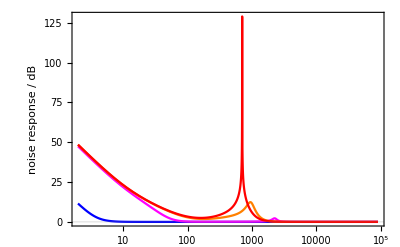
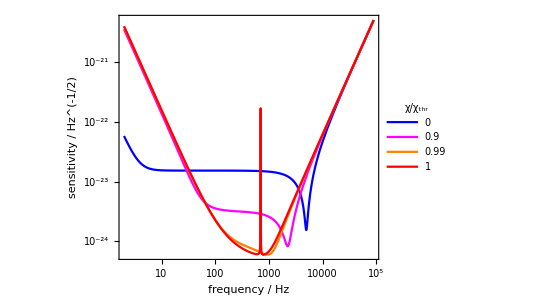
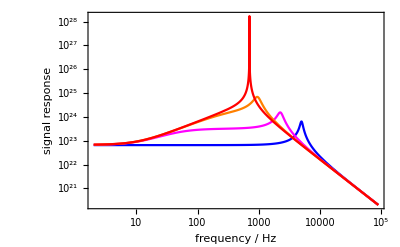
-Graphics- | -Graphics-
-Graphics- |

```mathematica
(*lossy on threshold*)
setConfigParamsLi2020[]
valsListList1={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{0.9HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{0.99HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
plotwReadoutCompact[valsListList1,"signal",None,{Blue,Magenta,Orange,Red},{2,9 10^4},"Quality",{{All,All},{1.1 10^20,All},{All,All}},65,{Style["0",FontFamily->"Monospace"],Style["0.9",FontFamily->"Monospace"],Style["0.99",FontFamily->"Monospace"],Style["1",FontFamily->"Monospace"]},Style["χ/χ_thr",FontFamily->"Monospace"],{0.4,0.75}]//Print
(*Export["nIS_on_threshold.pdf",%];*)
```

configuration parameters:
paramSetName=Li et al, 2020, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0.5 kHz, γcR/(2  π)=0 kHz, ωs/(2  π)=5. kHz; ωs/γbR=10.

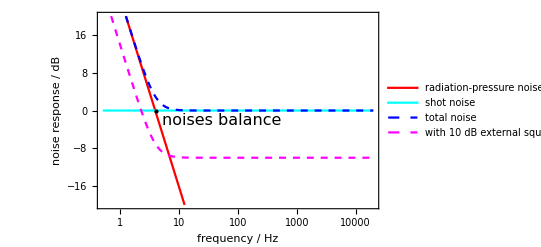

```mathematica
(*QN with external squeezing*)
setConfigParamsLi2020[]
printParams[]

SetOptions[LogLinearPlot,BaseStyle->FontSize->16];
plotQNExt[varsListList_,plotStyle_:{},fRange_:{2,9 10^4}]:=

LogLinearPlot[Evaluate[
{20Log10[Sqrt[QNFn[Join[{2π f},varsListList[[1]]//ReleaseHold]]^2-1]],
20Log10[QNFn[Join[{2π f},varsListList[[2]]//ReleaseHold]]],
20Log10[QNFn[Join[{2π f},varsListList[[1]]//ReleaseHold]]],Block[{extSqzFactor=1/10,ϕ=π/2},20Log10[singleReadoutSub[Re[Sqrt[SxComExtSqz11SignalRO]],Join[{2π f},varsListList[[1]]]//ReleaseHold]]]}],
{f,fRange[[1]],fRange[[2]]},ImageSize->400,PlotRange->{All,{-20,20}},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"noise response / dB",},{"frequency / Hz",}},
PerformanceGoal->"Speed",Axes->False,PlotLegends->Placed[LineLegend[{Red,Cyan,{Blue,Dashed},{Magenta,Dashed}},{"radiation-pressure noise","shot noise","total noise","with 10 dB external squeezing"},LabelStyle->Directive[14],Spacings->0.15],{0.6,0.8}]];
valsListList1={
{0,0,0,0,0,1},
{0,0,0,0,0,0}};
Show[plotQNExt[valsListList1,{Red,Cyan,{Blue,Dashed},{Magenta,Dashed}},{5 0.1,2 10^4}],Epilog->{
Black,PointSize[Large],Point[{1.4,0}],Text[Style["noises balance",16],Offset[{65,-10},{1.4,0}]]}]
Export[NotebookDirectory[]<>"QN_SQL_ext_sqz.pdf",%];
```

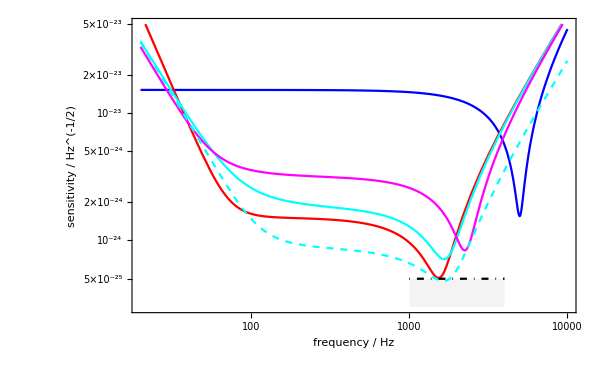

```mathematica
Clear[plotSensTarget]
plotSensTarget[varsListList_(*make sure that length matches the readout type*),readoutStr_,plotStyle_:{},fRange_:{2,9 10^4}]:=(
{fmin,fmax}=fRange;
ShFn=If[readoutStr=="signal",ASDShSignalReadout,If[readoutStr=="idler",ASDShIdlerReadout,Throw["plotwReadout: readoutStr not recognised"]]];
ShComExtSqz=If[readoutStr=="signal",ShComExtSqzSignalRO,If[readoutStr=="idler",ShComExtSqzIdlerRO,Throw["plotwReadout: readoutStr not recognised"]]];
Labeled[LogLogPlot[Evaluate[
Join[
Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}],
{Block[{extSqzFactor=1/10,ϕ=π/2},singleReadoutSub[Re[Sqrt[ShComExtSqz]],Join[{2π f},varsListList[[If[readoutStr=="idler",2,3]]]//ReleaseHold]]]},
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->600,PlotStyle->Join[plotStyle,{Directive[Black,DotDashed]}],PlotRange->{{fmin,fmax},{3 10^-25,5 10^-23}},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},
PerformanceGoal->"Quality",FrameTicksStyle->{{FontSize->14,},{FontSize->14,}},Filling->{Length[varsListList]+2->Bottom},FillingStyle->Directive[Opacity[0.3],LightGray]],{Framed[
Block[{legendOrder={1->3,2->1,3->2,4->4}},
LineLegend[Permute[Join[plotStyle[[2;;]],{Directive[Black,DotDashed]}],SparseArray[legendOrder]],Permute[Join[
{Apply[StringJoin,Map[ToString[#,StandardForm]&,{Style["χ/χ_thr=0.95,",FontFamily->"Monospace"]," optimistic losses"}]],
Apply[StringJoin,Map[ToString[#,StandardForm]&,{Style["χ/χ_thr=0.95,",FontFamily->"Monospace"]," realistic losses"}]],
Apply[StringJoin,Map[ToString[#,StandardForm]&,{Style["χ/χ_thr=0.90,",FontFamily->"Monospace"]," realistic losses"}]]}
(*Table[legendStylerSingleReadout[varsListList[[i]]],{i,1,Length[varsListList]}]*),{Apply[StringJoin,Map[ToString[#,StandardForm]&,{Style["χ/χ_thr=0.95,",FontFamily->"Monospace"], " realistic losses with 10 dB injected external squeezing"}]]},{"astrophysical target: 5×10^-25Hz^(-1/2) sensitivity at 1–4 kHz"}],SparseArray[legendOrder]]
,LabelStyle->Directive[14],LegendMarkerSize->{{25,15}}]],FrameStyle->Thin]},{Bottom},RotateLabel->True,LabelStyle->Directive[14,FontFamily->"Calibri Light"]])
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)0,(*γbR=*)2 π 500.,2 π 5000.]
valsListList1={
{0,75 10^-6,Tlb0,100 10^-6,Rpd0,1},
{0.95 HoldForm[singularityThr[75 10^-6,Tlb0,100 10^-6]],75 10^-6,Tlb0,100 10^-6,Rpd0,1},
{0.95 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1},
{0.90 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1}};
plotSensTarget[valsListList1,"signal",{Blue,Red,Cyan,Magenta,{Cyan,Dashed}},{2 10,10^4}]
Export["nIS_ideal_losses.pdf",%];
```

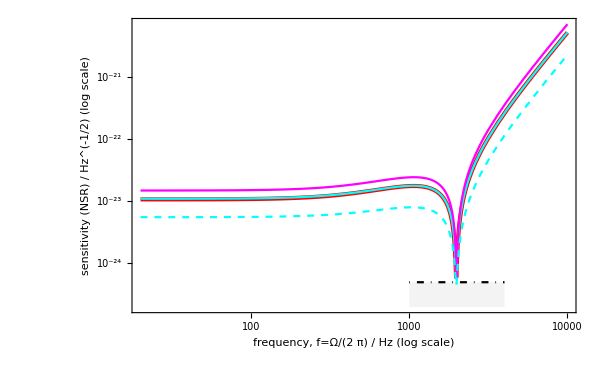

```mathematica
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)0,2π 2000.]
valsListList1={
{0.95HoldForm[singularityThr[75 10^-6,Tlb0,100 10^-6]],75 10^-6,Tlb0,100 10^-6,Rpd0,1},
{0.95 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1},
{0.7 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1}};
plotSensTarget[valsListList1,"idler",{{Red,Thickness[0.005]},Cyan,Magenta,{Cyan,Dashed}},{2 10,10^4}]
Export["nIS_idlerRO_ideal_losses.pdf",%];
```

```mathematica
valsListList1={
{0.95 HoldForm[singularityThr[75 10^-6,Tlb0,100 10^-6]],75 10^-6,Tlb0,100 10^-6,Rpd0,1},
{0.95 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1},
{0.90 HoldForm[singularityThr[100 10^-6,Tlb0,1000 10^-6]],100 10^-6,Tlb0,1000 10^-6,Rpd0,1}};
γbR0=0;
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},{
{2 π 500.,γbR0},
{2 π 5000.,γbR0},
{2 π 50000.,γbR0}},valsListList1,"idler",{Red,{Red,Dashed},Magenta},{1,10^5}]
```

```mathematica
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.]
printParams[]

(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1}*)
valsListList1={{0,Tla0,Tlb0,Tlc0,Rpd0,1},{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
plotwReadout[valsListList1,"idler"]
(*1/0 errors are caused by χ=0, since then no signal can enter the idler mode*)
```

configuration parameters:
paramSetName=Li et al, 2020 + idler sees SRM, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0.5 kHz, γcR/(2  π)=0.5 kHz, ωs/(2  π)=5. kHz; ωs/γbR=10.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(*idler readout reduces to nOPO*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)0,2 π 5000.]
valsListList1={
{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0},{0.95 HoldForm[singularityThr[1-10^-10000,Tlb0,Tlc0]],1-10^-10000,Tlb0,Tlc0,Rpd0,0}};
plotwReadout[valsListList1,"idler",None,{},{0.1,10^4}]
```

```mathematica
(*combined readout reduces to combined nOPO i.e. dOPO*)
(*{Ω,χ,γa,γbtot,γctot,Rpd,ρRP0or1,ϕ,ψ0,ψ1,ψ2}*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.]
Tla1=1-10^-100;
valsListListSlow1={{0,Tla1,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla1,Tlb0,Tlc0]],Tla1,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[1-10^-10000,Tlb0,Tlc0]],1-10^-10000,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/4}};
plotwReadout[valsListListSlow1,"combined",None,{},{0.1,10^4}]
Export["nIS_combinedRO_dOPO_limit.pdf",%];
```

$Aborted

```mathematica
(*idler readout has shot noise indep of pump phase? but RPN and signal are phase dependent*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)0,2 π 5000.]
valsListListSlow1={
{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,π/2,π/2,(*=ϕ=*)π/2,π/2},
{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,(3π)/4,π/2,(*=ϕ=*)π/2,π/2},
{0.95 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,π,π/2,(*=ϕ=*)π/2,π/2}};
plotwReadout[valsListListSlow1,"combined",None,{},{10^3,10^4}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

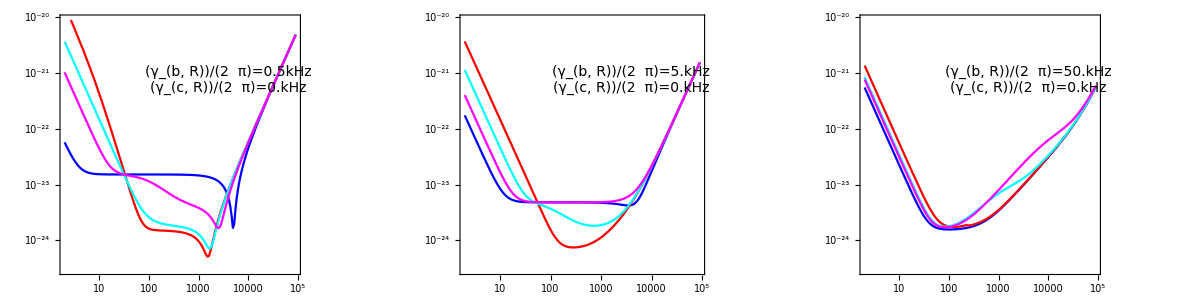
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},valsListList2,"signal",{Blue,Red,Orange,Magenta},{1,10^5}]*)
(*recovers previous plot, just remember that magenta line is at a different idler loss, previously at whatever γR for open SRM (see Tsrm) corresponds, now just 10000ppm*)
plotγbcRSensRow[{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},valsListList2,"signal",{Blue,Red,Cyan,Magenta},{2,9 10^4},{3 10^-25,9 10^-21},False(*sensitivity target*)]
```

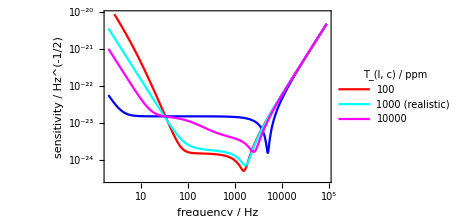

```mathematica
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)0,(*γbR=*)2 π 500.,(*ωs=*)2 π 5000.]
χRatio0=0.95;
Tla1=Tla0;
idlerLossList={100.,1000.,10000.} 10^-6;
valsListList2={
{0,Tla1,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[1]]]],Tla1,Tlb0,idlerLossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[2]]]],Tla1,Tlb0,idlerLossList[[2]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[3]]]],Tla1,Tlb0,idlerLossList[[3]],Rpd0,1}};
plotSensPretty[valsListList2,"signal",{Blue,Red,Cyan,Magenta},{2,9 10^4},{3 10^-25,9 10^-21},{"100"//monoS,
StringJoin[Map[ToString[#,StandardForm]&,{"1000"//monoS," (realistic)"}]],"10000"//monoS},"T_(l, c) / ppm"//monoS,True,True,{0.55,0.7}]
Export["nIS_sigRO_tolerance_Tlc.pdf",%];
```

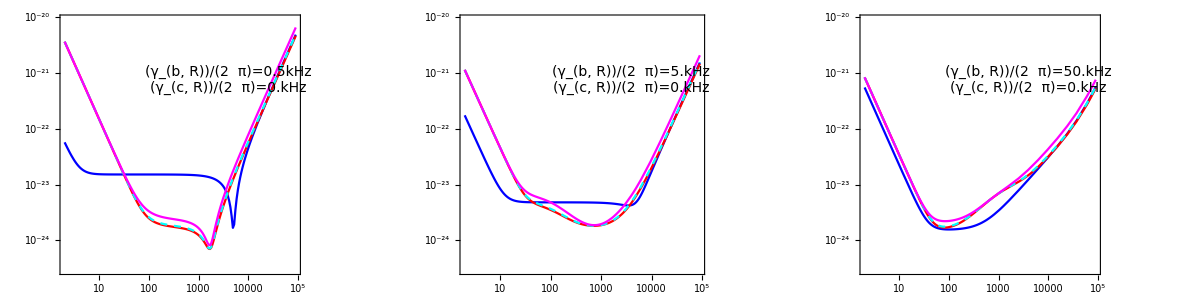
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},
valsListHeld,"signal",{Blue,Red,{Cyan,Dashed},Magenta},{2,9 10^4},{3 10^-25,9 10^-21},False(*sensitivity target*)]
```

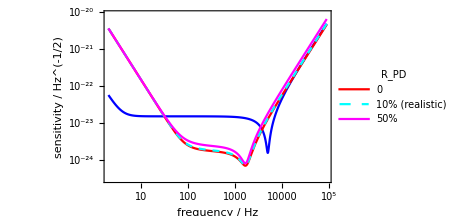

```mathematica
valsListHeld={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0.5,1}};
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)0,(*γbR=*)2 π 500.,(*ωs=*)2 π 5000.]
plotSensPretty[valsListHeld,"signal",{Blue,Red,{Cyan,Dashed},Magenta},{2,9 10^4},{3 10^-25,9 10^-21},{"0"//monoS,StringJoin[Map[ToString[#,StandardForm]&,{"10%"//monoS," (realistic)"}]],"50%"//monoS},"R_PD"//monoS,True,True,{0.55,0.7}]
Export["nIS_sigRO_tolerance_Rpd.pdf",%];
```

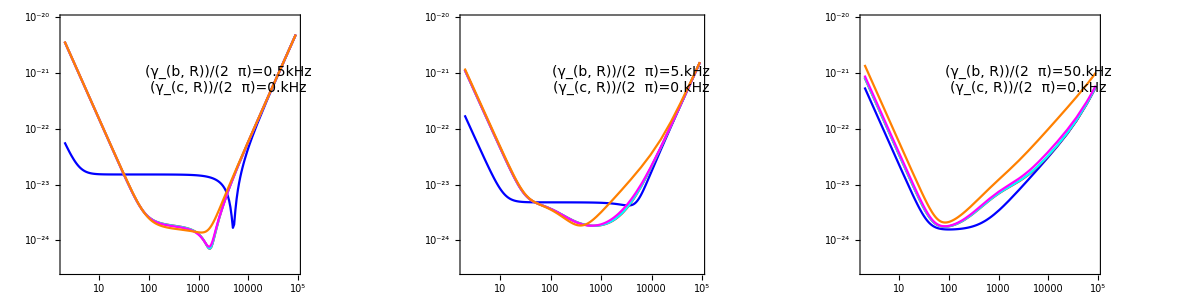
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},
valsListHeld,"signal",{Blue,Red,Cyan,Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},False(*sensitivity target*)]
```

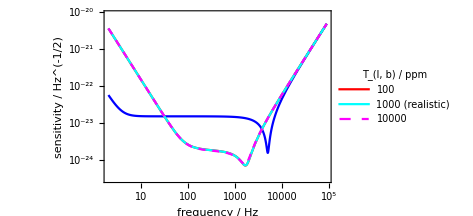

```mathematica
valsListHeld={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,0.1Tlb0,Tlc0]],Tla0,0.1Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,10Tlb0,Tlc0]],Tla0,10Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,100Tlb0,Tlc0]],Tla0,100Tlb0,Tlc0,Rpd0,1}};
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)0,(*γbR=*)2 π 500.,(*ωs=*)2 π 5000.]
plotSensPretty[{
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,0.1Tlb0,Tlc0]],Tla0,0.1Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,10Tlb0,Tlc0]],Tla0,10Tlb0,Tlc0,Rpd0,1}},"signal",{Blue,Red,Cyan,{Magenta,Dashed},Orange},{2,9 10^4},{3 10^-25,9 10^-21},{"100"//monoS,StringJoin[Map[ToString[#,StandardForm]&,{"1000"//monoS," (realistic)"}]],"10000"//monoS},"T_(l, b) / ppm"//monoS,True,True,{0.55,0.7}]
Export["nIS_sigRO_tolerance_Tlb.pdf",%];
```

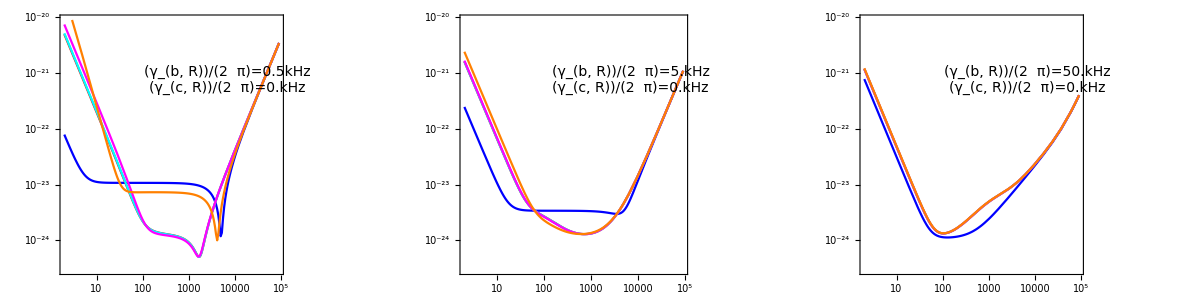
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
valsListHeld={
{0,Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[0.1Tla0,Tlb0,Tlc0]],0.1Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[10Tla0,Tlb0,Tlc0]],10Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[100Tla0,Tlb0,Tlc0]],100Tla0,Tlb0,Tlc0,Rpd0,1}};
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 0.,(*γbR=*)2 π 500.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 5000.},{(*γcR=*)2 π 0.,(*γbR=*)2 π 50000.}},
valsListHeld,"signal",{Blue,Red,Cyan,Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},False(*sensitivity target*)]
Export["nIS_sigRO_tolerance_Tla.pdf",%];
```

```mathematica
(*idler readout full tolerance to losses --> expand this group to see*)
```

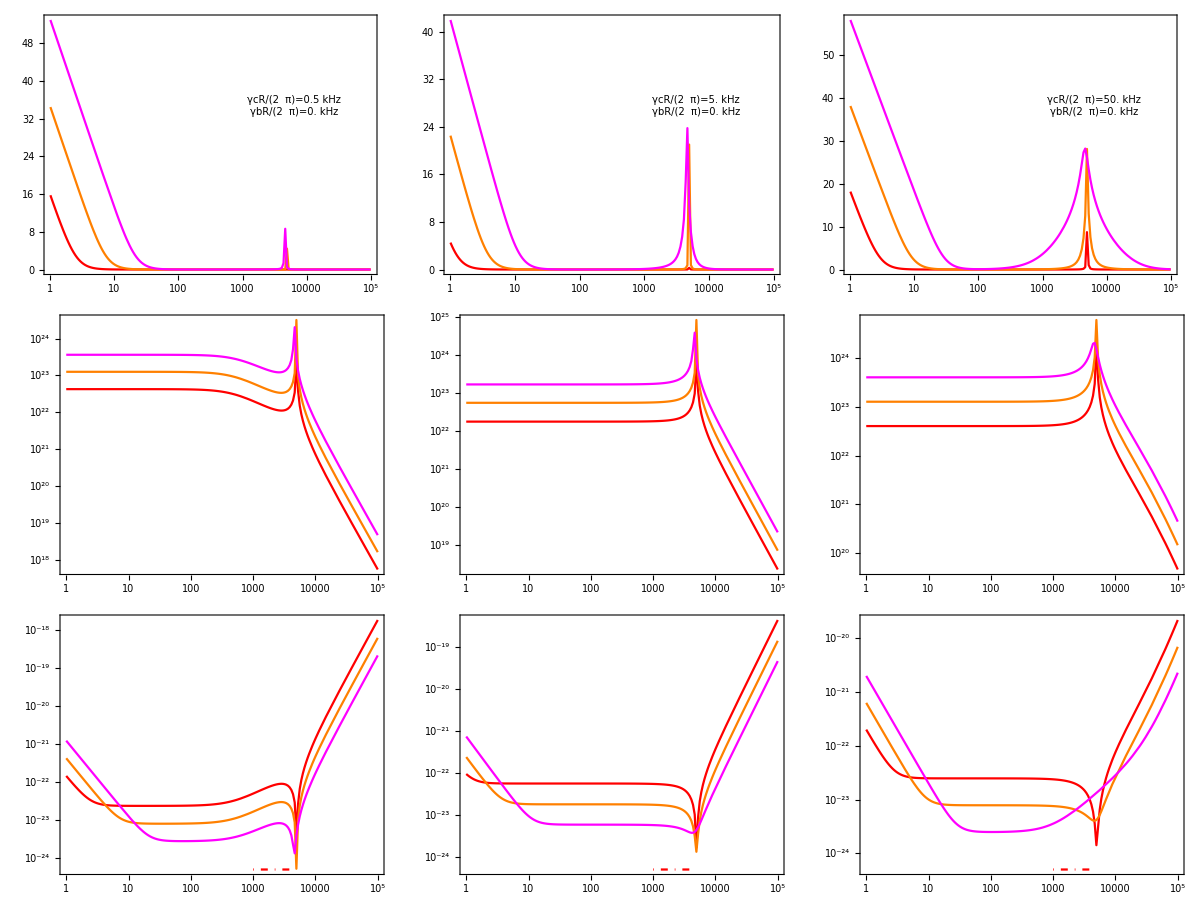
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 + idler sees SRM
readout: idler | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*idler readout behaves strangely against signal loss*)
Tla1=50 10^-6;
lossList={100.,1000.,10000.} 10^-6;
valsListList2={
{χRatio0 Hold[singularityThr[Tla1,lossList[[1]],Tlc0]],Tla1,lossList[[1]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[2]],Tlc0]],Tla1,lossList[[2]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[3]],Tlc0]],Tla1,lossList[[3]],Tlc0,Rpd0,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},valsListList2,"idler",{Red,Orange,Magenta},{1, 10^5}]
(*no χ=0 because then no signal in idler*)
(*NB: when γbR is zero τRTSRC is determined by Tsrm and γcR (unless Lsrm is given), else by γbR -- this is a fault with setting the derived parameters instead of the IFO parameters (e.g. Lsrm)*)
```

```mathematica
(*idler readout behaviour against signal loss: zoomed in, the peak does decrease but the broadband improvement is massive*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)0,2 π 5000.]
printParams[]
lossList={10.,100.,1000.,10000.,100000.,(1-10^-100)/10^-6} 10^-6;
(*Table index i is problematic inside Hold, be explicit (is annoying)*)
valsListList2={
{χRatio0 Hold[singularityThr[Tla1,lossList[[1]],Tlc0]],Tla1,lossList[[1]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[2]],Tlc0]],Tla1,lossList[[2]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[3]],Tlc0]],Tla1,lossList[[3]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[4]],Tlc0]],Tla1,lossList[[4]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[5]],Tlc0]],Tla1,lossList[[5]],Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,lossList[[6]],Tlc0]],Tla1,lossList[[6]],Tlc0,Rpd0,1}};
plotwReadout[valsListList2,"idler",None,Table[Blend[{Blue,Green},(i-1)/(Length[lossList]-1)],{i,1,Length[lossList]}],{4 10^3,6 10^3}]
```

Power::infy: Infinite expression 1/0 encountered.

configuration parameters:
paramSetName=Li et al, 2020 + idler sees SRM, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0 kHz, γcR/(2  π)=0.5 kHz, ωs/(2  π)=5. kHz; ωs/γbR=ComplexInfinity

```mathematica
(*for reference, the signal readout behaviour against idler loss watch that γa<γc still*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)0,(*γbR=*)2 π 500.,2 π 5000.]
printParams[]
lossList={100.,1000.,10000.,100000.,(1-10^-100)/10^-6} 10^-6;
valsListList2=
{{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[1]]]],Tla1,Tlb0,lossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[2]]]],Tla1,Tlb0,lossList[[2]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[3]]]],Tla1,Tlb0,lossList[[3]],Rpd0,1},{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[4]]]],Tla1,Tlb0,lossList[[4]],Rpd0,1},{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[5]]]],Tla1,Tlb0,lossList[[5]],Rpd0,1}};
plotwReadout[valsListList2,"signal",None,Table[Blend[{Blue,Green},(i-1)/(Length[lossList]-1)],{i,1,Length[lossList]}]]
```

configuration parameters:
paramSetName=Li et al, 2020 + idler sees SRM, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γbR/(2  π)=0.5 kHz, γcR/(2  π)=0 kHz, ωs/(2  π)=5. kHz; ωs/γbR=10.

```mathematica
(*testing other losses: detection*)
lossList={100.,1000.,10000.} 10^-6;
valsListList2={
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0.5,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},valsListList2,"idler",{Red,{Dashed,Magenta}},{1,10^5}]
```

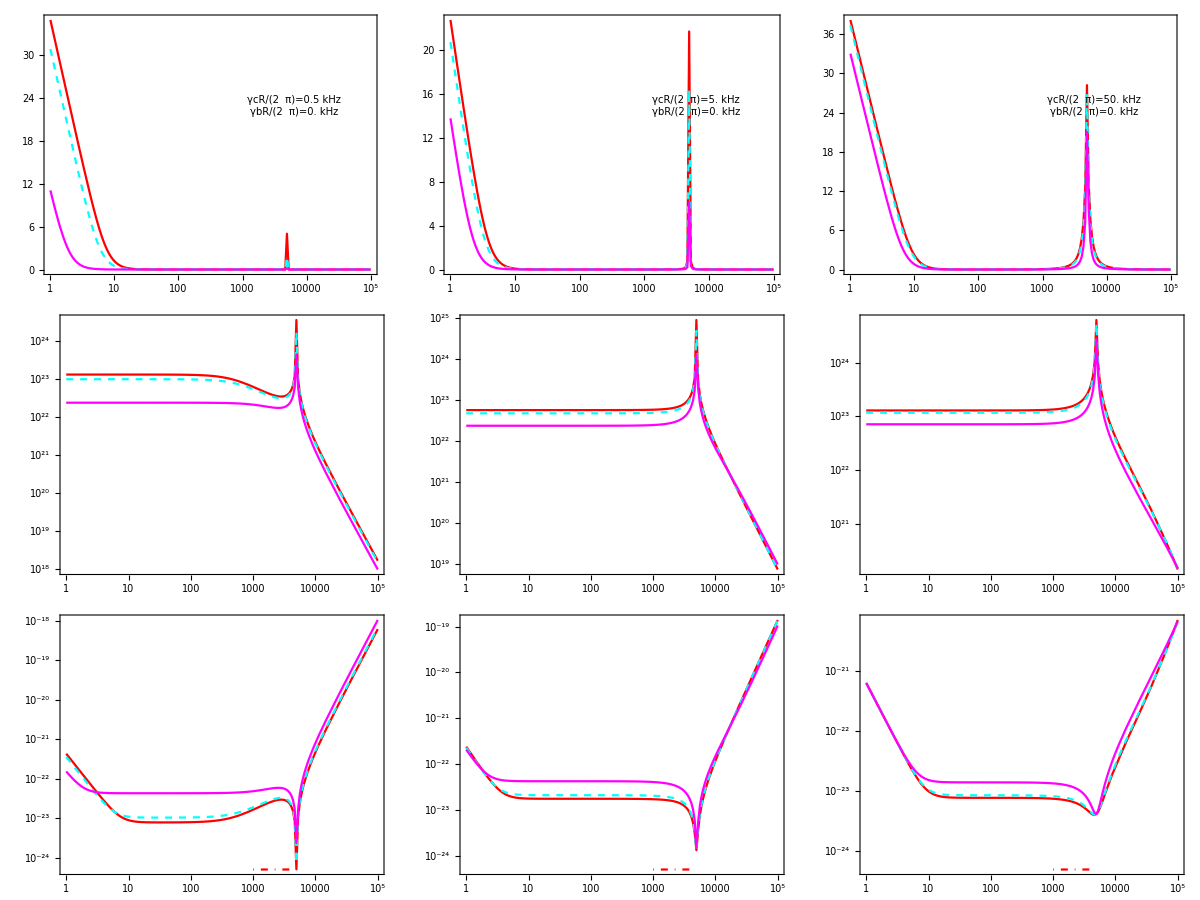
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 + idler sees SRM
readout: idler | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*testing other losses: idler intracavity*)
lossList={100.,10000.,100000.} 10^-6;
valsListList2={
{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[1]]]],Tla1,Tlb0,lossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[2]]]],Tla1,Tlb0,lossList[[2]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,lossList[[3]]]],Tla1,Tlb0,lossList[[3]],Rpd0,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},valsListList2,"idler",{Red,{Dashed,Cyan},Magenta},{1,10^5}]
```

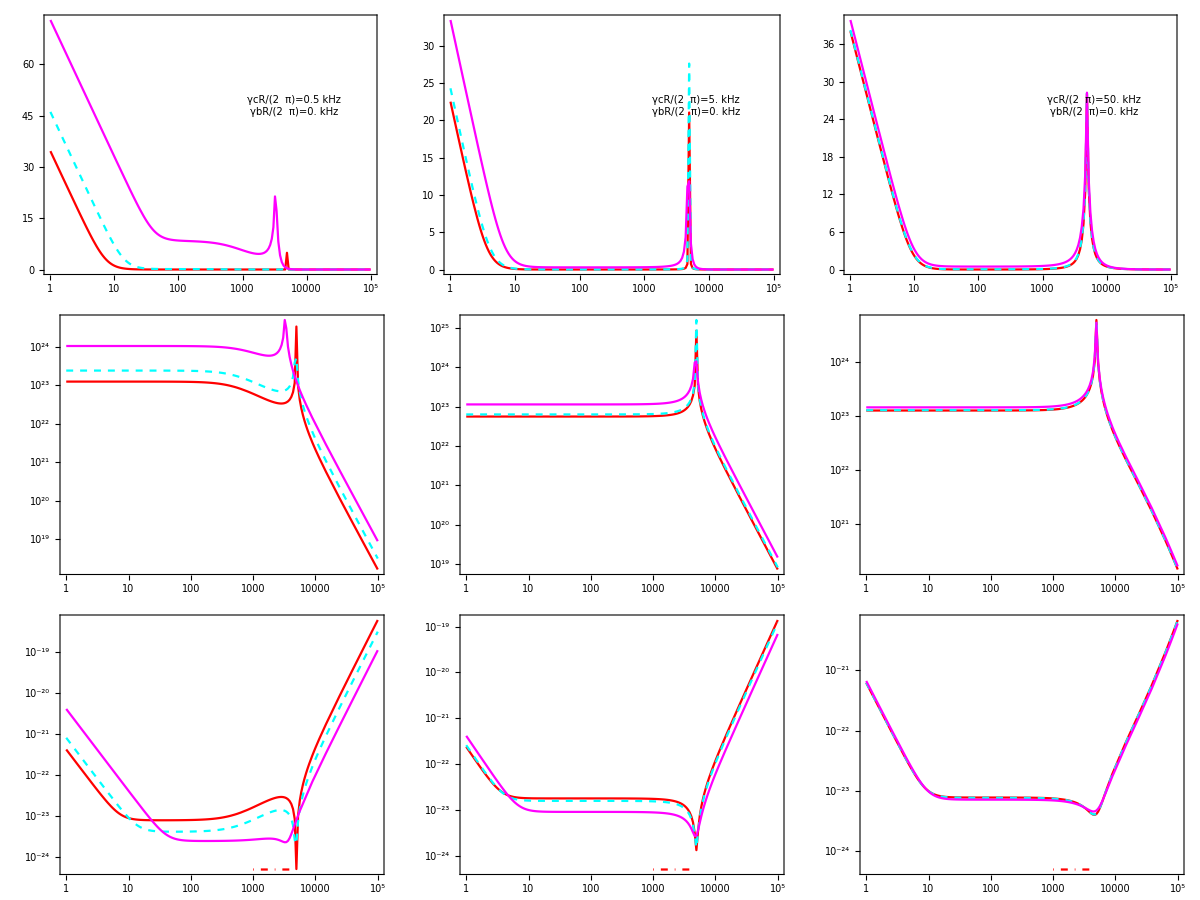
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 + idler sees SRM
readout: idler | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*testing other losses: arm intracavity*)
χRatio0=0.95;
lossList={100.,10000.,100000.} 10^-6;
valsListList2={
{χRatio0 Hold[singularityThr[lossList[[1]],Tlb0,Tlc0]],lossList[[1]],Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[lossList[[2]],Tlb0,Tlc0]],lossList[[2]],Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[lossList[[3]],Tlb0,Tlc0]],lossList[[3]],Tlb0,Tlc0,Rpd0,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},valsListList2,"idler",{Red,{Dashed,Cyan},Magenta},{1,10^5}]
```

```mathematica
valsListList2={
{0.95 Hold[singularityThr[Tla0,Tlb0,]],Tla1,Tlb0,lossList[[1]],Rpd0,1},
{0.95 Hold[singularityThr[Tla1,Tlb0,lossList[[2]]]],Tla1,Tlb0,lossList[[2]],Rpd0,1},
{0.9 Hold[singularityThr[Tla1,Tlb0,lossList[[3]]]],Tla1,Tlb0,lossList[[3]],Rpd0,1}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},valsListList2,"idler",{Red,{Dashed,Cyan},Magenta},{1,10^5}]
```

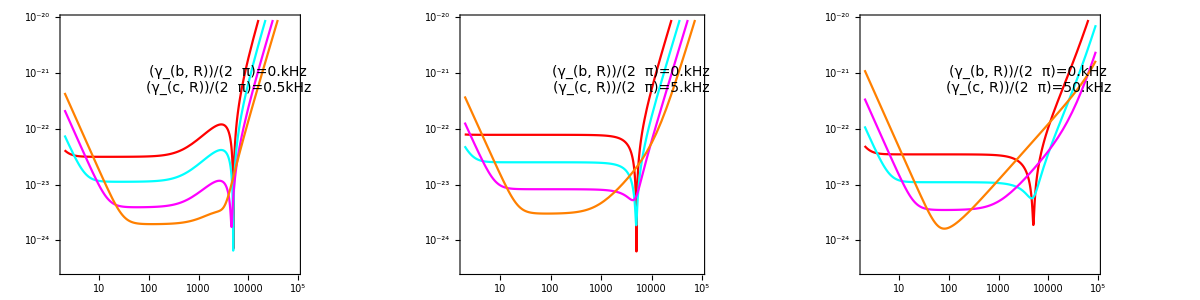
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},
valsListHeld,"idler",{Red,Cyan,Magenta,Orange},{2,9 10^4},{3. 10^-25,9. 10^-21},False(*sensitivity target*),150,"Quality"]
```

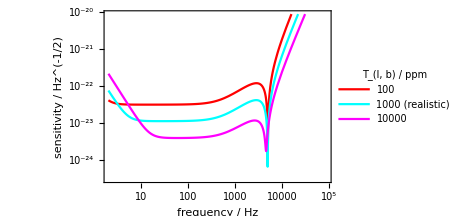

```mathematica
valsListHeld={
{χRatio0 Hold[singularityThr[Tla0,0.1Tlb0,Tlc0]],Tla0,0.1Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,10Tlb0,Tlc0]],Tla0,10Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,100Tlb0,Tlc0]],Tla0,100Tlb0,Tlc0,Rpd0,1}};
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)2 π 500.,(*γbR=*)0,(*ωs=*)2 π 5000.]
plotSensPretty[valsListHeld[[;;-2]],"idler",{Red,Cyan,Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},{"100"//monoS,StringJoin[Map[ToString[#,StandardForm]&,{"1000"//monoS," (realistic)"}]],"10000"//monoS},"T_(l, b) / ppm"//monoS,False,True,{0.35,0.7}]
Export["nIS_idlerRO_tolerance_Tlb.pdf",%];
```

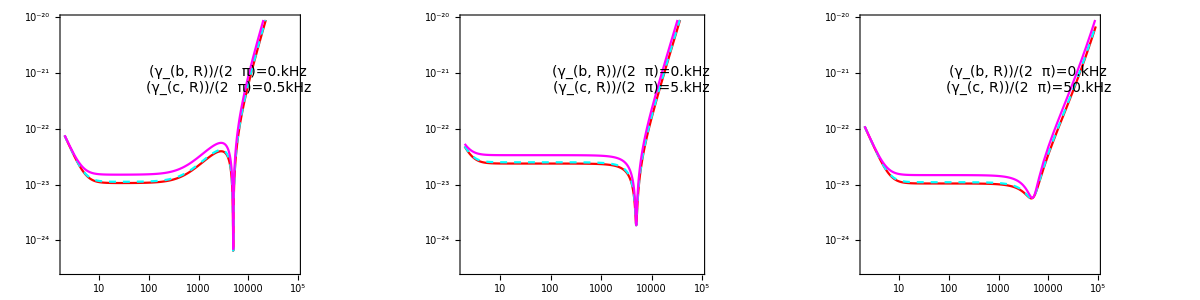
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},
valsListHeld,"idler",{Red,{Cyan,Dashed},Magenta,Orange},{2,9 10^4},{3. 10^-25,9. 10^-21},False(*sensitivity target*),150,"Quality"]
```

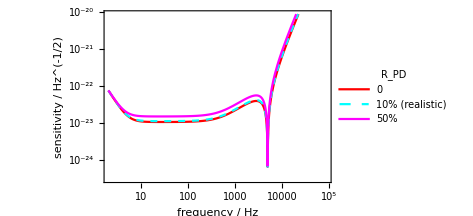

```mathematica
valsListHeld={
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,0.5,1}};setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)2 π 500.,(*γbR=*)0,(*ωs=*)2 π 5000.]
plotSensPretty[valsListHeld,"idler",{Red,{Cyan,Dashed},Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},{"0"//monoS,StringJoin[Map[ToString[#,StandardForm]&,{"10%"//monoS," (realistic)"}]],"50%"//monoS},"R_PD"//monoS,False,True,{0.35,0.7}]
Export["nIS_idlerRO_tolerance_Rpd.pdf",%];
```

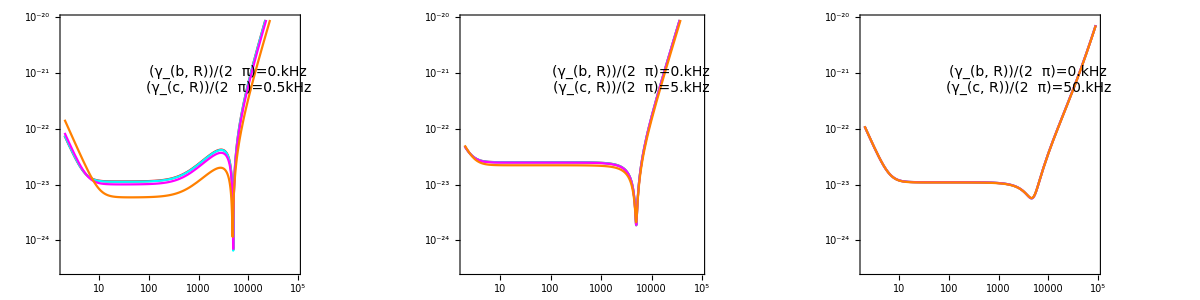
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
valsListHeld={
{χRatio0 Hold[singularityThr[0.1Tla0,Tlb0,Tlc0]],0.1Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[10Tla0,Tlb0,Tlc0]],10Tla0,Tlb0,Tlc0,Rpd0,1},
{χRatio0 Hold[singularityThr[100Tla0,Tlb0,Tlc0]],100Tla0,Tlb0,Tlc0,Rpd0,1}};
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},
valsListHeld,"idler",{Red,Cyan,Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},False(*sensitivity target*),150,"Quality"]
Export["nIS_idlerRO_tolerance_Tla.pdf",%];
```

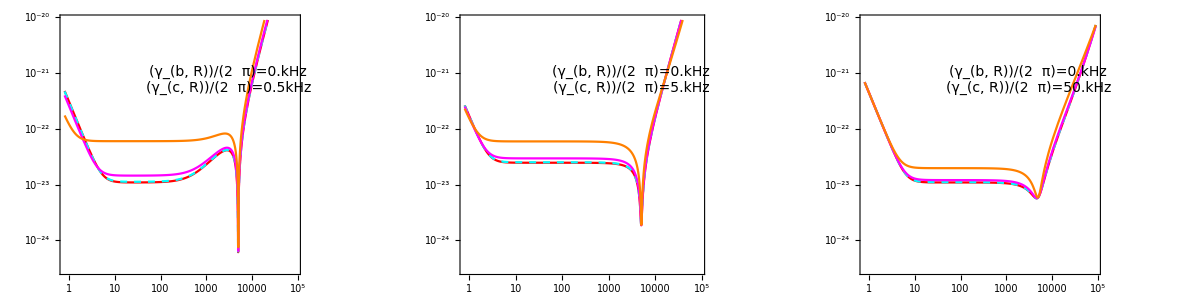
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 500.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 5000.,(*γbR=*)2 π 0.},{(*γcR=*)2 π 50000.,(*γbR=*)2 π 0.}},
valsListHeld,"idler",{Red,{Cyan,Dashed},Magenta,Orange},{0.8,9 10^4},{3. 10^-25,9. 10^-21},False(*sensitivity target*),150,"Quality"]
```

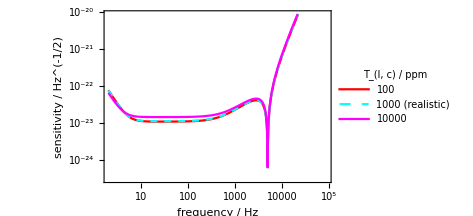

```mathematica
idlerLossList={100.,1000.,10000.,100000.} 10^-6;
valsListHeld={
{χRatio0 Hold[singularityThr[Tla0,Tlb0,idlerLossList[[1]]]],Tla0,Tlb0,idlerLossList[[1]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,idlerLossList[[2]]]],Tla0,Tlb0,idlerLossList[[2]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,idlerLossList[[3]]]],Tla0,Tlb0,idlerLossList[[3]],Rpd0,1},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,idlerLossList[[4]]]],Tla0,Tlb0,idlerLossList[[4]],Rpd0,1}};
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)2 π 500.,(*γbR=*)0,(*ωs=*)2 π 5000.]
plotSensPretty[valsListHeld[[;;-2]],"idler",{Red,{Cyan,Dashed},Magenta,Orange},{2,9 10^4},{3 10^-25,9 10^-21},{"100"//monoS,StringJoin[Map[ToString[#,StandardForm]&,{"1000"//monoS," (realistic)"}]],"10000"//monoS},"T_(l, c) / ppm"//monoS,False,True,{0.35,0.7}]
Export["nIS_idlerRO_tolerance_Tlc.pdf",%];
```

```mathematica
(*tolerance of combined readout to losses*)
χRatio0=0.95;
Tla1=0.5Tla0;
lossList={100000.} 10^-6;
valsListListSlow1={{0,Tla1,Tlb0,Tlc0,Rpd0,1,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla1,Tlb0,Tlc0]],Tla1,Tlb0,Tlc0,Rpd0,1,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[Tla1,lossList[[1]],Tlc0]],Tla1,lossList[[1]],Tlc0,Rpd0,1,π/2,π/2,(*=ϕ=*)π/2,π/4},
{0.95 HoldForm[singularityThr[Tla1,Tlb0,lossList[[1]]]],Tla1,Tlb0,lossList[[1]],Rpd0,1,π/2,π/2,(*=ϕ=*)π/2,π/4}};
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.]
plotwReadout[valsListListSlow1,"combined"]
```

```mathematica
(*lossless plots*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.]
lowLoss=1. 10^-10;
valsListList0={{0,lowLoss/10,lowLoss,lowLoss,lowLoss,1,π/2,π/2,(*=ϕ=*)π/2,π/4},{0.95 HoldForm[singularityThr[lowLoss/10,lowLoss,lowLoss]],lowLoss/10,lowLoss,lowLoss,lowLoss,1,π/2,π/2,(*=ϕ=*)π/2,π/4}};
plotwReadout[valsListList0,"combined"]
```

```mathematica
Clear[plotDualReadoutγbcRGridPretty]
plotDualReadoutγbcRGridPretty[configParams_(*γcR,γbR don't matter*),γRList_(*{{γcR1,γbR1},...}*),varsListList_(*make sure that length matches the readout type*),plotStyle_:{},fRange_:{1,10^5},yRanges_:{{-5,59},{5 10^20,9 10^24},{3 10^-25,7 10^-21}}]:=(
{fmin,fmax}=fRange;
{QNFn1,sigFn1,ShFn1}={QNSignalReadout,sigSignalReadout,ASDShSignalReadout};
{QNFn2,sigFn2,ShFn2}={QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout};
{p1List,p2List,p3List}={{},{},{}};
noiseRange=yRanges[[1]];
sigRange=yRanges[[2]];
sensRange=yRanges[[3]];
imageSize=130;
performanceGoal="Speed";
Do[
setConfigParamsCustom@@ReplacePart[configParams,{-3->γRList[[j]][[1]](*γcR*),-2->γRList[[j]][[2]](*γbR*)}];
p1=LogLinearPlot[Evaluate[Flatten[Table[
{20Log10[QNFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]]],
20Log10[QNFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->{Automatic,imageSize},
ImagePadding->If[j==1,{{45,7},{1,1}},{{1,7},{1,1}}],TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},noiseRange},PlotStyle->plotStyle,Frame->True,FrameTicksStyle->Directive[14],GridLines->{{},{0}},
PerformanceGoal->performanceGoal,Epilog->Text[Style[StringForm["γcR/(2  π)=`` kHz\nγbR/(2  π)=`` kHz",NumberForm[(γRList[[j]][[1]])/(2π)10^-3],NumberForm[(γRList[[j]][[2]])/(2π)10^-3]],14,FontFamily->"Monospace"],Scaled[{0.70,0.75}],Background->Opacity[0.5,Lighter[LightGray]]]];
p2=LogLogPlot[Evaluate[Flatten[Table[
{sigFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
sigFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->{Automatic,imageSize},ImagePadding->If[j==1,{{45,7},{1,1}},{{1,7},{1,1}}],TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},sigRange},PlotStyle->plotStyle,Frame->True,FrameTicksStyle->Directive[14],
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Join[Flatten[
Table[
{ShFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
ShFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->{Automatic,imageSize+20(*add the extra image padding*)},ImagePadding->If[j==1,{{45,7},{20,1}},{{1,7},{20,1}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[2Length[varsListList],Length[plotStyle]],{0,2Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Black,DotDashed]}]),PlotRange->{{fmin,fmax},sensRange},Filling->{2 Length[varsListList]+1->Bottom},FillingStyle->Directive[Opacity[0.3],LightGray],Frame->True,FrameTicksStyle->Directive[14],
PerformanceGoal->performanceGoal];
AppendTo[p1List,p1];
AppendTo[p2List,p2];
AppendTo[p3List,p3];
,{j,1,Length[γRList]}];
Labeled[Grid[{p1List,p2List,p3List},Spacings->0],{Grid[{{"sensitivity (NSR)", "signal response", "noise response"}, {"/ Hz^(-1/2) (log scale)", "/ (log scale)", "/ dB (20 log_10)"}},Spacings->3],Grid[{{"frequency, f=Ω/(2  π) / Hz (log scale)"},{Framed[LineLegend[({q0,r0}=If[plotStyle≠{},QuotientRemainder[2Length[varsListList],Length[plotStyle]],{0,2Length[varsListList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Black,DotDashed]}]),Join[Flatten[Table[
{Apply[StringJoin,Map[ToString[#,StandardForm]&,{"signal readout: ",legendStylerSingleReadout[varsListList[[i]]]}]],
Apply[StringJoin,Map[ToString[#,StandardForm]&,{"idler readout:   ",legendStylerSingleReadout[varsListList[[i]]]}]]},{i,1,Length[varsListList]}]],{"astrophysical target: 5×10^-25Hz^(-1/2) sensitivity at 1–4 kHz"}],LabelStyle->Directive[14],LegendMarkerSize->{{25,15}}],FrameStyle->Thin]}}]},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[14,FontFamily->"Calibri Light"]])
```

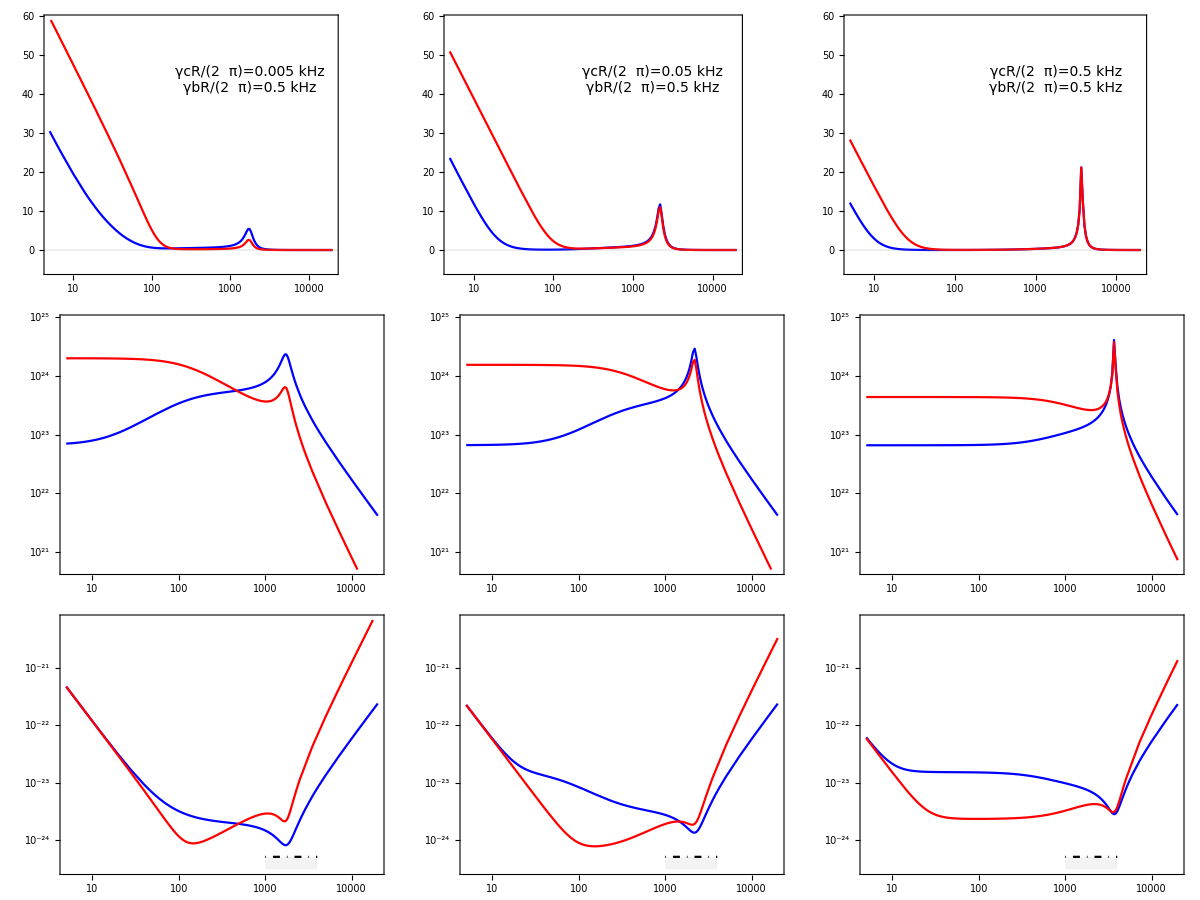
-Graphics-sensitivity (NSR) | signal response | noise response
/ Hz^(-1/2) (log scale) | / (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*overlay signal and idler separate readouts for the same parameters, (*γcR=*)2 π 500.,(*γbR=*)2 π 500. (and could vary them up and down separately)
--> can't actually use both readouts at once due to collapsing the correlations between the entangled modes?*)
χRatio1=0.95;
valsListList1={
{χRatio1 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
γbR0=2π 500.;
plotDualReadoutγbcRGridPretty[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + changed idler/signal readout",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 5.,γbR0},
{(*γcR=*)2 π 50.,γbR0},
{(*γcR=*)2 π 500.,γbR0}},valsListList1,{Blue,Red},(*{fmin,fmax}*){5 10^0,2 10^4}]
(*hypothesis: peak moves because the singularity frequency is increasing, this looks correct!*)
(*change frequency range to 0.01 to 10^5 to see RP effects, change to 10^3 to 10^4 to see peak motion (and compare against threshold plot)*)
```

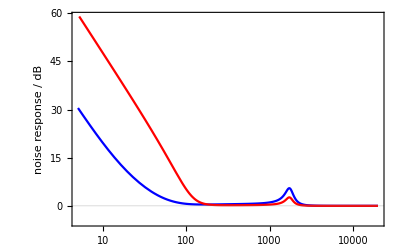
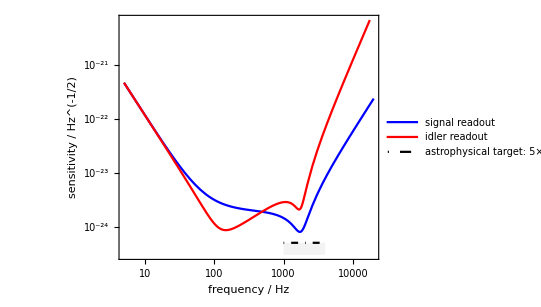
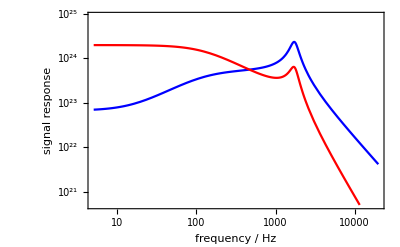
-Graphics- | -Graphics-
-Graphics- |

```mathematica
plotSignalVsIdler[varsListList_,legendLabels_,plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:100]:=(
{fmin,fmax}=fRange;
{QNFn1,sigFn1,ShFn1}={QNSignalReadout,sigSignalReadout,ASDShSignalReadout};
{QNFn2,sigFn2,ShFn2}={QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout};
p1=LogLinearPlot[Evaluate[Flatten[Table[
{20Log10[QNFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]]],
20Log10[QNFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{leftPad,10},{1,All}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",14],},{,plotLabel}},
PerformanceGoal->performanceGoal,GridLines->{{},{0}}];
p2=LogLogPlot[Evaluate[Flatten[Table[
{sigFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
sigFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{1,1}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",14],},{,}},
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Join[Flatten[
Table[
{ShFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
ShFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{All,1}},PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}},PlotStyle->
Join[plotStyle,{Directive[Black,DotDashed]}],Filling->{2 Length[varsListList]+1->Bottom},FillingStyle->Directive[Opacity[0.3],LightGray]];
Labeled[Column[{p1,p2,p3},Spacings->0],
{LineLegend[Join[plotStyle,{Directive[Black,DotDashed]}],legendLabels,LabelStyle->Directive[13],LegendMarkerSize->{{25,15}}]},{Right}])

Clear[plotSignalVsIdlerCompact]
plotSignalVsIdlerCompact[varsListList_(*make sure that length matches the readout type*),legendLabels_:None,plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:65,legendTitle_:None]:=(
{fmin,fmax}=fRange;
{QNFn1,sigFn1,ShFn1}={QNSignalReadout,sigSignalReadout,ASDShSignalReadout};
{QNFn2,sigFn2,ShFn2}={QNIdlerReadout,sigIdlerReadout,ASDShIdlerReadout};
imageHeight=150;
bottomPad=55;
rightPad=11;
p1=LogLinearPlot[Evaluate[Flatten[Table[
{20Log10[QNFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]]],
20Log10[QNFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight},
ImagePadding->{{leftPad,rightPad},{1,1}},FrameTicksStyle->{{Directive[Black],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",16,Black],},{,}},
PerformanceGoal->performanceGoal,GridLines->{{},{0}}];
p2=LogLogPlot[Evaluate[Flatten[Table[
{sigFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
sigFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]]],
{f,fmin,fmax},ImageSize->{Automatic,imageHeight+bottomPad},ImagePadding->{{leftPad,rightPad},{bottomPad,1}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,20,30}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}}(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*),FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",Black],},{Style["frequency / Hz",Black],}},
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Join[Flatten[
Table[
{ShFn1[Join[{2π f},varsListList[[i]]//ReleaseHold]],
ShFn2[Join[{2π f},varsListList[[i]]//ReleaseHold]]},{i,1,Length[varsListList]}]],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->{Automatic,2imageHeight+bottomPad},AspectRatio->1/1.3,ImagePadding->{{leftPad+15,rightPad},{bottomPad,1}},PlotStyle->
Join[plotStyle,{Directive[Black,DotDashed]}],Filling->{2 Length[varsListList]+1->Bottom},FillingStyle->Directive[Opacity[0.3],LightGray],PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",Black],},{Style["frequency / Hz",Black],}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,-25,-20}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{Directive[Black],},{Directive[Black],}},PlotLegends->Placed[LineLegend[
Join[plotStyle,{Directive[Black,DotDashed]}],
If[legendLabels===None,Table[If[readoutStr=="combined",legendStylerComReadoutSplit,legendStylerSingleReadoutSplit][varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels],LegendLabel->legendTitle,LabelStyle->Directive[18],LegendMarkerSize->{{25,15}},Spacings->0.15],{0.5,0.8}]];
Grid[{{p1,Item[p3,Alignment->Center]},{p2,SpanFromAbove}},Spacings->0(*,Frame->All*)])

setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,(*γcR=*)2 π 5.,(*γbR=*)2π 500.,(*ωs=*)2 π 5000.]
plotSignalVsIdlerCompact[{{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}},{"signal readout","idler readout",Text[Style["astrophysical target:\n5×10^-25Hz^(-1/2) sensitivity at 1–4 kHz",LineSpacing->{1,0}]]},None,{Blue,Red},{5 10^0,2 10^4},"Quality",{{-5,59},{5 10^20,9 10^24},{3 10^-25,7 10^-21}}]//Print
(*Export["nIS_signal_vs_idler_ROs.pdf",%];*)
```

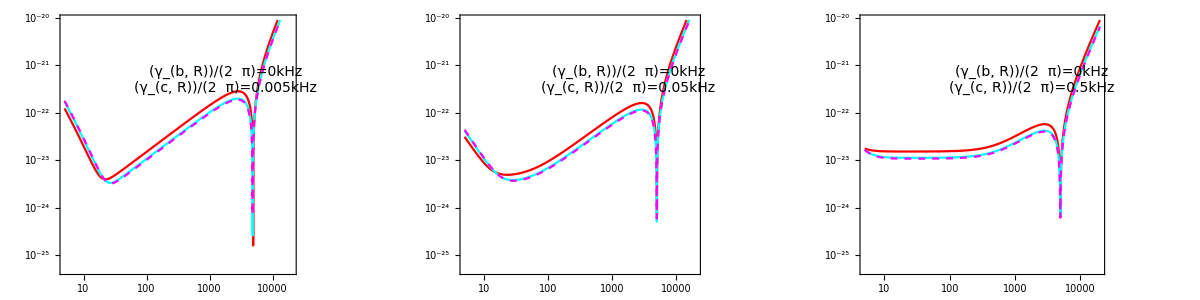
-Graphics-sensitivity (NSR)
/ Hz^(-1/2) (log scale)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*Tolerance to pump power. Showing the effect of changing the ratio to threshold by plus/minus 4%.*)
χRatio0=0.95;
ΔχRatio=0.04;(*4%*)
(*valsListList1={
{(χRatio0-ΔχRatio)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(χRatio0)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(χRatio0+ΔχRatio)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
γbR0=2π 500.;
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 5.,γbR0},
{(*γcR=*)2 π 50.,γbR0},
{(*γcR=*)2 π 500.,γbR0}},
valsListList1,"idler",{Red,Cyan,Magenta,Orange},{5 10^0,2 10^4},{3. 10^-25,9. 10^-21},False(*sensitivity target*),150,"Speed"]*)
valsListList1={
{(0.70)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(0.95)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(0.99)Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
γbR0=0;
plotγbcRSensRow[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)2 π 500.,2 π 5000.},
{{(*γcR=*)2 π 5.,γbR0},
{(*γcR=*)2 π 50.,γbR0},
{(*γcR=*)2 π 500.,γbR0}},
valsListList1,"idler",{Red,Cyan,{Magenta,Dashed},Orange},{5 10^0,2 10^4},{5 10^-26,9. 10^-21},False(*sensitivity target*),150,"Quality"]
Export["nIS_idlerRO_tolerance_chi.pdf",%];
```

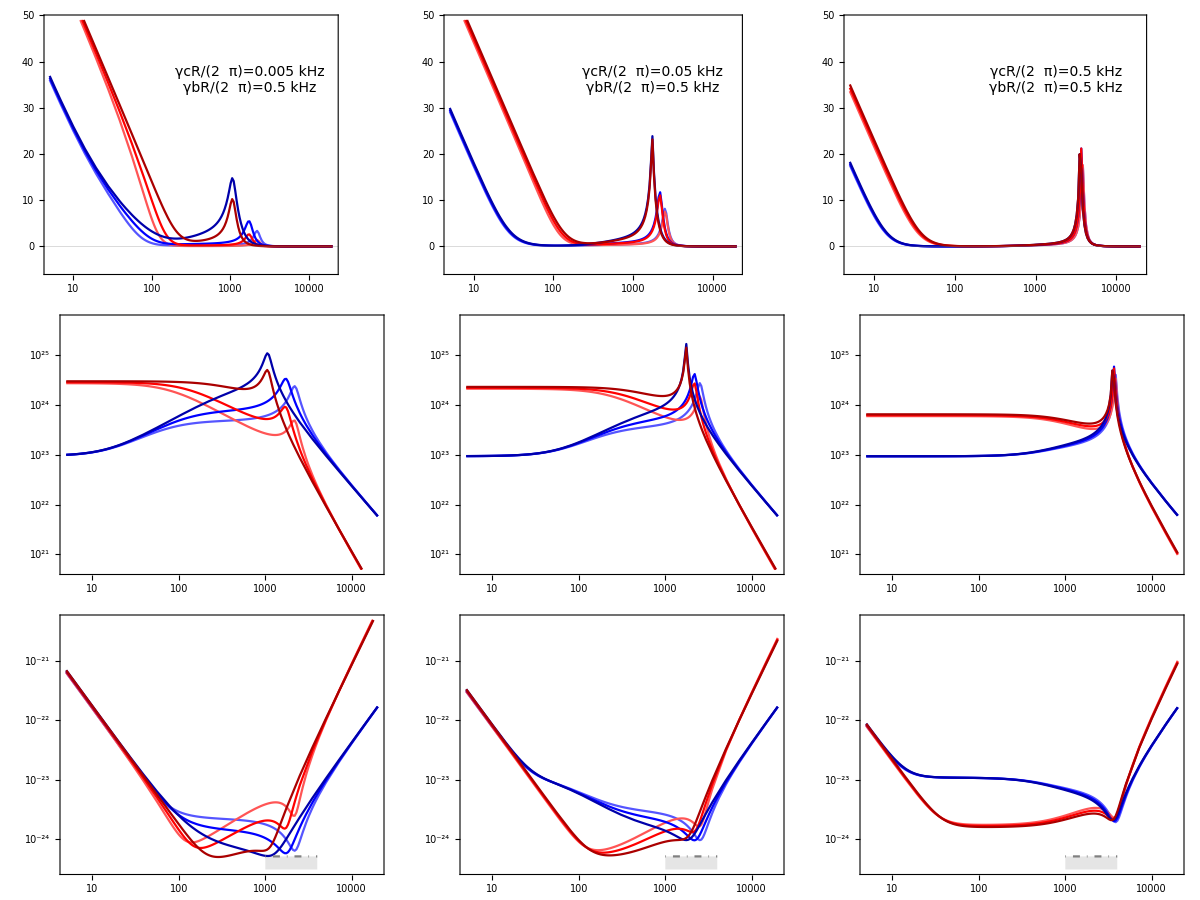
-Graphics-sensitivity (NSR) | signal response | noise response
/ Hz^(-1/2) (log scale) | / (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
ΔχRatio=0.04;(*4%*)
valsListList1={
{(χRatio1-ΔχRatio) Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(χRatio1) Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},
{(χRatio1+ΔχRatio) Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1}};
γbR0=2π 500.;
plotDualReadoutγbcRGridPretty[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + changed idler/signal readout",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 5.,γbR0},
{(*γcR=*)2 π 50.,γbR0},
{(*γcR=*)2 π 500.,γbR0}},valsListList1,{Lighter[Blue],Lighter[Red],Blue,Red,Darker[Blue],Darker[Red]},{5 10^0,2 10^4},{{-5,49},{5 10^20,5 10^25},{3 10^-25,5 10^-21}}]
Export["nIS_ROs_tolerance_chi.pdf",%];
```

```mathematica
γR0=γbR0;
plotDualReadoutγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + changed idler/signal readout",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{γR0,2 π 5.},
{γR0,2 π 50.},
{γR0,2 π 500.},
{γR0,2 π 5000.}},valsListList1,{Lighter[Red],Lighter[Cyan],Red,Cyan,Darker[Red],Darker[Cyan]},{10^1,10^4}]
Export["nIS_ROs_tolerance_chi_large_idlerROrate.pdf",%];
```

```mathematica
(*ticks not working for some reason*)
plotCombPretty[varsListList_(*make sure that length matches the readout type*),plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},performanceGoal_:"Quality",yRanges_:{{All,All},{All,All},{All,All}},leftPad_:100,legendLabels_:None]:=(
{fmin,fmax}=fRange;
{QNFn,sigFn,ShFn}={QNComReadout,sigComReadout,ASDShComReadout};
p1=LogLinearPlot[Evaluate[Table[20Log10[QNFn[Join[{2π f},varsListList[[i]]//ReleaseHold]]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{leftPad,10},{1,All}},FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[1]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["noise response / dB",14],},{,plotLabel}},
PerformanceGoal->performanceGoal,GridLines->{{},{0}}];
p2=LogLogPlot[Evaluate[Table[sigFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{1,1}},FrameTicks->{{Block[{ticks=Table[{10^i,Superscript[10,i]},{i,20,25}]},
Join[ticks,Flatten[Table[{k*j,Null},{k,2,9},{j,ticks[[All,1]]}],1]]],None},{Automatic,None}}(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*),FrameTicksStyle->{{Directive[FontSize->14],},{Directive[FontOpacity->0,FontSize->0],}},PlotRange->{{fmin,fmax},yRanges[[2]]},PlotStyle->plotStyle,Frame->True,FrameLabel->{{Style["signal response",14],},{,}},
PerformanceGoal->performanceGoal];
p3=LogLogPlot[Evaluate[Table[ShFn[Join[{2π f},varsListList[[i]]//ReleaseHold]],{i,1,Length[varsListList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{leftPad,10},{All,1}},PlotStyle->plotStyle,PlotRange->{{fmin,fmax},yRanges[[3]]},Frame->True,FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},FrameTicks->{{Automatic,None},{Automatic,None}},
PerformanceGoal->performanceGoal,FrameTicksStyle->{{FontSize->14,},{FontSize->14,}}];
Labeled[Column[{p1,p2,p3},Spacings->0],
{LineLegend[plotStyle,
If[legendLabels===None,Table[legendStylerComReadoutSplit[varsListList[[i]]],{i,1,Length[varsListList]}],legendLabels],LabelStyle->Directive[13],LegendMarkerSize->{{25,15}}]},{Right}])
```

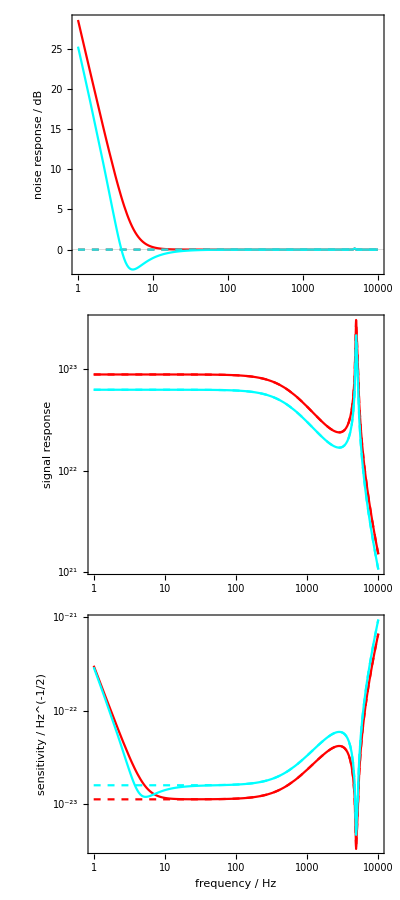

```mathematica
χRatio1=0.95;
Δϕ=π/4;
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",(*γcR=*)2 π 500.,(*γbR=*)0,2 π 5000.]
valsListListSlow1={
{χRatio1 singularityThr[Tla0,Tlb0,Tlc0],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 singularityThr[Tla0,Tlb0,Tlc0],Tla0,Tlb0,Tlc0,Rpd0,0,(*ϕ=*)(π/2),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 singularityThr[Tla0,Tlb0,Tlc0],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2+Δϕ),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 singularityThr[Tla0,Tlb0,Tlc0],Tla0,Tlb0,Tlc0,Rpd0,0,(*ϕ=*)(π/2+Δϕ),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2}};
plotwReadoutPretty[valsListListSlow1,"combined",None,{Red,{Red,Dashed},Cyan,{Cyan,Dashed},Orange},{1,10^4},"Speed",{{All,All},{All,All},{All,2 10^-21}},100,{Style["ρ≠0, ϕ=π/2,  ψ_1=π/2",FontFamily->"Monospace"],Style["ρ=0, ϕ=π/2,  ψ_1=π/2",FontFamily->"Monospace"],Style["ρ≠0, ϕ=(3  π)/4, ψ_1=π/2",FontFamily->"Monospace"],Style["ρ=0, ϕ=(3  π)/4, ψ_1=π/2",FontFamily->"Monospace"]}]
```

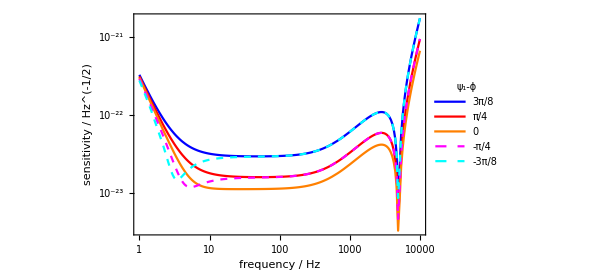

```mathematica
ϕList={π/8,(2π)/8,(4π)/8,(6π)/8,(7π)/8};(*{π/8,(2π)/8,(3π)/8,(4π)/8,(5π)/8,(6π)/8,(7π)/8};*)
valsListListSlow1=Table[{χRatio0 singularityThr[Tla0,Tlb0,Tlc0],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)ϕList[[i]],π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},{i,1,Length[ϕList]}];
plotSensPretty[valsListListSlow1,"combined",
{Blue,Red,Orange,{Magenta,Dashed},{Cyan,Dashed}},{1,10^4},{All,All},{"3π/8"//monoS,"π/4"//monoS,"0"//monoS,"-π/4"//monoS,"-3π/8"//monoS},"ψ_1-ϕ"//monoS,False,True,{0.5,0.7},"Speed",450]
Export["nIS_idlerRO_tolerance_phi.pdf",%];
```

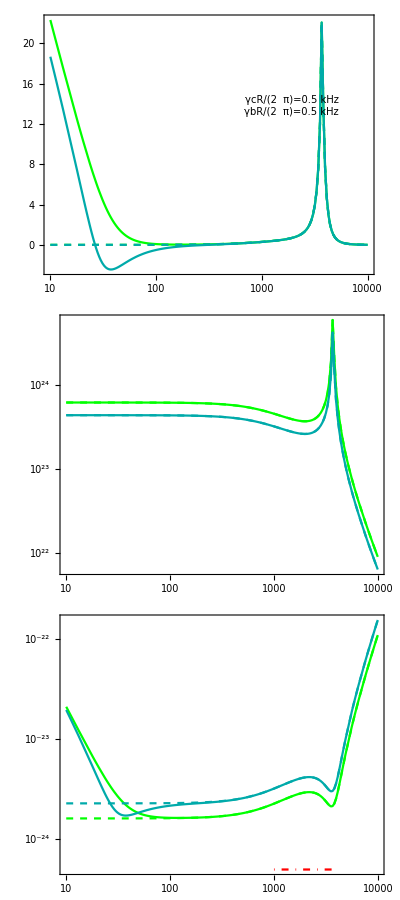
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 + idler readout rate
readout: combined | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*squeezing appears in the above plots, check this (1) without radiation pressure noise, (2) if there are idler-idler covariances, (3) if only anti-sqz in the separate idler quadratures, (4) if there is squeezing in the signal combinations*)
(*without RP*)
valsListListSlow1={
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,(*ϕ=*)(π/2),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2+Δϕ),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,(*ϕ=*)(π/2+Δϕ),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler readout rate",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,γbR0}},valsListListSlow1,"combined",{Green, {Green,Dashed},Darker[Cyan],{Darker[Cyan],Dashed}},{10,10^4}]
```

```mathematica
(*separate idler quadratures, if psi1=phi-pi/2 then there is no signal*)
valsListListSlow1={
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2-Δϕ),π/2,(*ψ1=*)π/2,(*ψ2=*)π/2},
{χRatio1 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(π/2-Δϕ),π/2,(*ψ1=*)0,(*ψ2=*)π/2}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler readout rate",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2 π 500.,γbR0}},valsListListSlow1,"combined",{Green, Darker[Cyan]},{10,10^4}]
```

```mathematica
(*check signal combinations, only signal is in 2nd quadrature --> why is it not seen in signal?
if suspicion is correct and it is due to ponderomotive, then squeezer shouldn't matter*)
ϕ1=π/2;
valsListListSlow1={
{0 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(ϕ1),(*ψ0=*)π/2,(*ψ1=*)π/2,(*ψ2=*)0},
{0 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1,(*ϕ=*)(ϕ1),(*ψ0=*)π/4,(*ψ1=*)π/2,(*ψ2=*)0},
{0 HoldForm[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,0,(*ϕ=*)(ϕ1),(*ψ0=*)π/4,(*ψ1=*)π/2,(*ψ2=*)0}};
plotγbcRGrid[{2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler readout rate",(*γcR=*)None,(*γbR=*)None,2 π 5000.},
{{(*γcR=*)2π 500.,2π 500.}},valsListListSlow1,"combined",{Green,Darker[Cyan], {Dashed,Darker[Cyan]}},{1,10^4}]
```

```mathematica
(*idler noise budget*)
RpdIdler[varsList_]:=singleReadoutSub[Re[Sqrt[(Rpd C24.ConjugateTranspose[C24])[[1,1]]/.idlerReadout]],varsList]
RinIdler[varsList_]:=singleReadoutSub[Re[Sqrt[(C24.Rin.ConjugateTranspose[Rin].ConjugateTranspose[C24])[[1,1]]/.idlerReadout]],varsList]
RaIdler[varsList_]:=singleReadoutSub[Re[Sqrt[(C24.Ra.ConjugateTranspose[Ra].ConjugateTranspose[C24])[[1,1]]/.idlerReadout]],varsList]
RbIdler[varsList_]:=singleReadoutSub[Re[Sqrt[(C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])[[1,1]]/.idlerReadout]],varsList]
(*split SRC losses into signal and idler losses*)
RbsigIdler[varsList_]:=singleReadoutSub[Re[Sqrt[((C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])[[1,1]]/.idlerReadout)/.{γctot->γcR}]],varsList]
RbidlIdler[varsList_]:=singleReadoutSub[Re[Sqrt[((C24.Rb.ConjugateTranspose[Rb].ConjugateTranspose[C24])[[1,1]]/.idlerReadout)/.{γbtot->γbR}]],varsList]

Clear[plotNoiseBudgetIdlerPretty]
plotNoiseBudgetIdlerPretty[varsList_,plotStyle_,fRange_:{1,10^5},performanceGoal_:"Speed"]:=
LogLinearPlot[Evaluate[{
20Log10[RinIdler@Join[{2π f},varsList//ReleaseHold]],
20Log10[RaIdler@Join[{2π f},varsList//ReleaseHold]],
20Log10[RbsigIdler@Join[{2π f},varsList//ReleaseHold]],
20Log10[RbidlIdler@Join[{2π f},varsList//ReleaseHold]],
20Log10[RpdIdler@Join[{2π f},varsList//ReleaseHold]],
20Log10[QNIdlerReadout@Join[{2π f},varsList//ReleaseHold]]}],{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"readout port vacuum","arm intra-cavity loss","signal intra-cavity loss","idler intra-cavity loss","detection loss","total quantum noise"},LabelStyle->Directive[14],LegendLabel->legendStylerSingleReadoutSplit[varsList//ReleaseHold]],PlotRange->All,PlotStyle->Join[plotStyle,{Directive[Black,Dashed]}],Frame->True,FrameTicksStyle->Directive[FontSize->14],FrameLabel->{{Style["noise response\n/ dB (20log_10)",14],},{Style["frequency, f=Ω/(2  π) / Hz (log scale)",14],}},PerformanceGoal->performanceGoal]
```

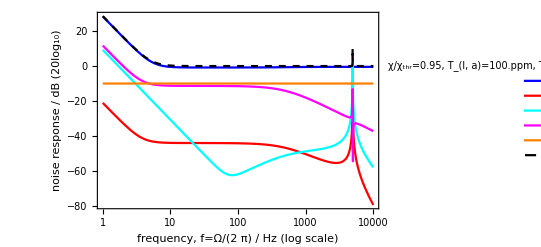

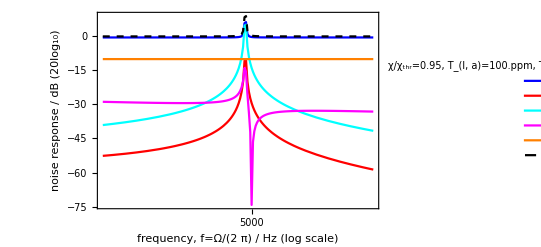

```mathematica
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + idler sees SRM",(*γcR=*)2 π 500.,(*γbR=*)0,2 π 5000.]
χRatio0=0.95;
plotNoiseBudgetIdlerPretty[{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},{Blue,Red,Cyan,Magenta,Orange},{1,10^4},"Quality"]
Export["nIS_idlerRO_noise_budget.pdf",%];
plotNoiseBudgetIdlerPretty[{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0]],Tla0,Tlb0,Tlc0,Rpd0,1},{Blue,Red,Cyan,Magenta,Orange},{4 10^3,6 10^3},"Speed"]
```